```mathematica
$CustomTicksPath = SetDirectory["C:\\Users\\novar\\Dropbox\\scripts\\math_nb\\CustomTicks"];
<<CustomTicks`
SetOptions[LogTicks,LogPlot->True,MajorTickLength->0.02,MinorTickLength->0.01];
SetOptions[LinTicks,MajorTickLength->0.02,MinorTickLength->0.01];
```

## Preparation functions

```mathematica
decayprobability[τ_,distance_,decaylength_]:=Quiet[ⅇ^(-(decaylength+distance)/τ) (-1+ⅇ^(decaylength/τ))]
kfactor=3.0;
averageboostfactor=6.0;
InverseEVtoMeter=0.2*10^-6;
rapiditytogamma[y_]:=1/2Sqrt[2+Exp[-2y]+Exp[2y]]
gammatorapidityPzonly[γ_]:=1/2 Log[(1+Sqrt[1-1/γ^2])/(1-Sqrt[1-1/γ^2])]
rapiditytogammabeta[y_]:=Sqrt[rapiditytogamma[y]^2-1]
averageboostfactorfunc[x_]:=Interpolation[{#[[1]],#[[4]]}&/@ggpdf,InterpolationOrder->1][x]+1/2Log[(teamenergy+protonmass+Sqrt[teamenergy^2-protonmass^2])/(teamenergy+protonmass-Sqrt[teamenergy^2-protonmass^2])]
metaprime=957.78*10^-3;
```

```mathematica
Solve[γ==1/Sqrt[1-β^2],β]
```

{{β→-(√(-1+γ^2))/γ},{β→(√(-1+γ^2))/γ}}

## Lifetime-M_a plot

```mathematica
WidthMaeV={{0.06101467495104318,0.001092360057946684},{0.07145879167371805,0.001886082856529087},{0.08288204433914359,0.003055275240744163},{0.09316297173802668,0.004915490999034501},{0.10115924860382464,0.007952302849178956},{0.10801320020308003,0.01358789367288134},{0.12108647825351149,0.030775608136111746},{0.1217211034015907,0.08795205984070696},{0.12210187849043819,0.06261246900447423},{0.12971738026738866,0.010305793554064345},{0.13120874936537485,0.0021486120173530086},{0.13139279065831777,0.0035134248920267817},{0.1366751796181479,0.0009914667752252367},{0.14710610932475887,0.0020526933785943394},{0.1528177356574717,0.00328809174269905},{0.16284481299712295,0.00542294792753641},{0.17541039092909116,0.008606539764508134},{0.1936875951937721,0.013579164685326993},{0.2131071247249957,0.020472834321932372},{0.2359536300558469,0.03076053228782612},{0.25994246065324067,0.04527984447601117},{0.28393129125063454,0.0658483716611192},{0.30906244711457087,0.09446965733614814},{0.3341936029785072,0.13584499241536585},{0.35932475884244364,0.19852851009132383},{0.38445591470637996,0.29080785056538955},{0.40730242003723116,0.4319187251126691},{0.42443729903536964,0.6635825113048992},{0.44042985276696545,1.0583112486799366},{0.4552800812320188,1.6733161407484718},{0.4689879844305296,2.701924946815279},{0.48269588762904025,4.462802831661535},{0.4918344897613808,7.113085326886795},{0.5009730918937213,11.337266013326168},{0.5091978338128277,20.500865189134114},{0.5158233203587747,32.46376583782562},{0.5203926214249449,54.05079646655601},{0.52267727195803,87.83185724971321},{0.5266373328820443,147.1849606889925},{0.5268404129294296,243.85780296033138},{0.5281350482315111,408.26711752199327},{0.5353697749196141,9461.616601558131},{0.5371467253342358,1332.940049023701},{0.5377813504823149,755.1868583818181},{0.5446353020815703,407.6102741665233},{0.5474276527331189,244.61770497154475},{0.5500930783550514,145.0956120568042},{0.5546623794212217,53.419598015815986},{0.5603740057539345,31.85559198401852},{0.5672279573531899,19.35345661066635},{0.5763665594855304,11.758250415228193},{0.587789812150956,7.284029782063863},{0.6026400406160092,4.6233801325980775},{0.6232018954137754,3.036228456689305},{0.6517600270773395,2.2101744527122476},{0.6871721103401588,2.035677212206167},{0.7225841936029783,2.2584618844850413},{0.7568539515992551,2.637848356572229},{0.791123709595532,3.088096612641593},{0.8196818412590962,4.172067173868072},{0.8368167202572344,6.586040298996421},{0.8482399729226601,10.772852912180529},{0.856236249788458,17.47858015103571},{0.864232526654256,28.82103190795785},{0.8710864782535114,45.78708070002618},{0.8779404298527668,79.12646288597118},{0.8847943814520222,130.68395644398743},{0.890506007784735,215.65808719928782},{0.8962176341174476,357.61655088612287},{0.9019292604501604,595.424170714163},{0.9064985615163307,983.3671207878889},{0.9110678625825009,1650.5658752337965},{0.9156371636486712,2748.1223411535143},{0.9179218141817563,4465.6638745793925},{0.9224911152479266,7617.82804713234},{0.9247757657810117,12631.824356595309},{0.9260450160771702,21576.477996478952},{0.9356913183279741,1.492075752410487*^6},{0.9369605686241326,193862.52037022123},{0.9378490438314432,58536.8746000322},{0.9383567439499066,102812.03192823388},{0.9497799966153323,25441.85779360961},{0.955618547977661,15381.839496936747},{0.9658994753765441,9380.758231692142},{0.9876036554408526,6380.367199523697},{1.023015738703672,6105.116133416894},{1.053858520900321,7735.792602949731},{1.0812743272973426,10895.106191927634},{1.1052631578947367,15854.93304973265},{1.1281096632255876,23512.076683809424},{1.1520984938229817,34961.86100976697},{1.1795143002200033,49013.216536455606},{1.2080724318835672,66294.21227473745},{1.2389152140802162,87015.65749205618},{1.2697579962768653,110448.87317263908},{1.3028854290065999,136045.61685623656},{1.336012861736334,165313.89407629013},{1.370282619732611,196007.35800745696},{1.404552377728888,228669.07655295098},{1.4399644609917073,258504.8745337518},{1.4753765442545266,282436.7004373795},{1.5119309527838887,296609.99364837306},{1.547343036046708,307110.96261202474},{1.58389744457607,317345.2586014868},{1.6193095278388894,317473.2573130415},{1.6558639363682515,317605.4391677541},{1.6924183448976136,306997.12546658015},{1.7278304281604329,285138.6877107935},{1.7632425114232522,257665.07666911042},{1.798654594686072,230695.43317421127},{1.8340666779488912,208106.38962724686},{1.8694787612117105,214418.11218182798},{1.9048908444745298,217312.17889303752},{1.9334489761380942,223175.0965222965}}
```

{{0.0610147,0.00109236},{0.0714588,0.00188608},{0.082882,0.00305528},{0.093163,0.00491549},{0.101159,0.0079523},{0.108013,0.0135879},{0.121086,0.0307756},{0.121721,0.0879521},{0.122102,0.0626125},{0.129717,0.0103058},{0.131209,0.00214861},{0.131393,0.00351342},{0.136675,0.000991467},{0.147106,0.00205269},{0.152818,0.00328809},{0.162845,0.00542295},{0.17541,0.00860654},{0.193688,0.0135792},{0.213107,0.0204728},{0.235954,0.0307605},{0.259942,0.0452798},{0.283931,0.0658484},{0.309062,0.0944697},{0.334194,0.135845},{0.359325,0.198529},{0.384456,0.290808},{0.407302,0.431919},{0.424437,0.663583},{0.44043,1.05831},{0.45528,1.67332},{0.468988,2.70192},{0.482696,4.4628},{0.491834,7.11309},{0.500973,11.3373},{0.509198,20.5009},{0.515823,32.4638},{0.520393,54.0508},{0.522677,87.8319},{0.526637,147.185},{0.52684,243.858},{0.528135,408.267},{0.53537,9461.62},{0.537147,1332.94},{0.537781,755.187},{0.544635,407.61},{0.547428,244.618},{0.550093,145.096},{0.554662,53.4196},{0.560374,31.8556},{0.567228,19.3535},{0.576367,11.7583},{0.58779,7.28403},{0.60264,4.62338},{0.623202,3.03623},{0.65176,2.21017},{0.687172,2.03568},{0.722584,2.25846},{0.756854,2.63785},{0.791124,3.0881},{0.819682,4.17207},{0.836817,6.58604},{0.84824,10.7729},{0.856236,17.4786},{0.864233,28.821},{0.871086,45.7871},{0.87794,79.1265},{0.884794,130.684},{0.890506,215.658},{0.896218,357.617},{0.901929,595.424},{0.906499,983.367},{0.911068,1650.57},{0.915637,2748.12},{0.917922,4465.66},{0.922491,7617.83},{0.924776,12631.8},{0.926045,21576.5},{0.935691,1.49208×10^6},{0.936961,193863.},{0.937849,58536.9},{0.938357,102812.},{0.94978,25441.9},{0.955619,15381.8},{0.965899,9380.76},{0.987604,6380.37},{1.02302,6105.12},{1.05386,7735.79},{1.08127,10895.1},{1.10526,15854.9},{1.12811,23512.1},{1.1521,34961.9},{1.17951,49013.2},{1.20807,66294.2},{1.23892,87015.7},{1.26976,110449.},{1.30289,136046.},{1.33601,165314.},{1.37028,196007.},{1.40455,228669.},{1.43996,258505.},{1.47538,282437.},{1.51193,296610.},{1.54734,307111.},{1.5839,317345.},{1.61931,317473.},{1.65586,317605.},{1.69242,306997.},{1.72783,285139.},{1.76324,257665.},{1.79865,230695.},{1.83407,208106.},{1.86948,214418.},{1.90489,217312.},{1.93345,223175.}}

#### Rescaling from eV to GeV units and from f_a=1/(32 Pi^2) TeV to f_a=1000 TeV

```mathematica
WidthMaGeV=Transpose@{WidthMaeV[[All,1]],WidthMaeV[[All,2]]/10^9*(1/(32 Pi^2*1000))^2};
WidthMaGeVFunc=Interpolation[WidthMaGeV,InterpolationOrder->1];
```

#### Calculation of lifetime using running α_s

```mathematica
mu=2.2/1000;
md=4.7/1000;
ms=20*md;
mc=1.275;
mb=4.18;
mt = 172.4;
mPi=135/1000;
mK=497/1000;
Mz=91.1876;
Mz=91.18;
GammaZ=2.495;
Mw=80.379;

GF=1.166 10^(-5);
ThetawatMz = ArcSin[Sqrt[0.231]];
v=Sqrt[1/(Sqrt[2]GF)];

g2atMz=2 Mz Cos[ThetawatMz]/v;
gpatMz = g2atMz Tan[ThetawatMz];
g1atMz=Sqrt[5/3]gpatMz;
alpha1atMz = g1atMz^2/4/Pi;
alpha2atMz = g2atMz^2/4/Pi;

b1=41/10;
b2=-19/6;

alpha1[μ_]:=1/(1/alpha1atMz-b1/(2Pi)Log[μ/Mz]);
alpha2[μ_]:=1/(1/alpha2atMz-b2/(2Pi)Log[μ/Mz]);
alphaEM[mu_]:=3/5alpha1[mu]alpha2[mu]/(alpha2[mu]+3/5alpha1[mu]);

LambdaQCD=0.48;
Nf[μ_]:=4(*using 4 quark flavors*)
beta0[μ_]=11-2/3Nf[μ];
beta1[μ_] = 102-38/3Nf[μ];
z[mu_]:=-beta0[mu]^2/E/beta1[mu](LambdaQCD^2/mu^2)^(beta0[mu]^2/beta1[mu]);

alphas[μ_]:=-4Pi beta0[μ]/beta1[μ]/ProductLog[-1,z[μ]];(* using the expression in 1604.08082v3 eq. 3.21 *)
```

```mathematica
nflav=3;
EA=(97/4-7/6nflav);
KggNNLO[ma_,c3_,fa_]:=1+alphas[ma]/Pi EA+(alphas[ma]/Pi)^2EA(3/4 EA+(51/8-19/24nflav)/(11/4-nflav/6));
KggNLO[ma_]:=1+alphas[ma]/Pi EA;
GammaaglugluNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNLO[ma];
GammaaglugluNNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNNLO[ma,c3,fa];
(*This is in GeV*)
LifetimeinmmNLO[ma_,c3_,fa_]:=1/GammaaglugluNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
LifetimeinmmNNLO[ma_,c3_,fa_]:=1/GammaaglugluNNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
```

```mathematica
Widthfunc[ma_]:=Piecewise[{{WidthMaGeVFunc[ma],ma<=1.82},{GammaaglugluNLO[ma,1,1000*1000],ma>1.82}}];
```

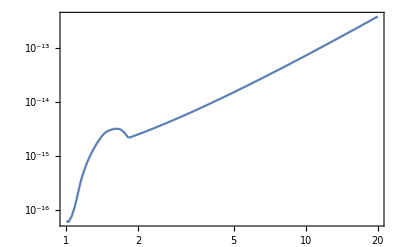

```mathematica
LogLogPlot[Widthfunc[ma],{ma,1,20},Frame->True]
```

#### Decay width into photons

```mathematica
c2=1;c1=1;
GammaPhoton[ma_,fa_]:=alphaEM[ma]^2/(256 Pi^3)ma^3/fa^2(c2+5/3 c1);
```

```mathematica
GeVtocm={{1/5.06*10^-21," ",{0.02,0},{}},{1/5.06*10^-20,"10^7",{0.02,0},{}},{1/5.06*10^-19," ",{0.02,0},{}},{1/5.06*10^-18," ",{0.02,0},{}},{1/5.06*10^-17,"10^4",{0.02,0},{}},{1/5.06*10^-16," ",{0.02,0},{}},{1/5.06*10^-15," ",{0.02,0},{}},{1/5.06*10^-14,"10",{0.02,0},{}},{1/5.06*10^-13," ",{0.02,0},{}},{1/5.06*10^-12," ",{0.02,0},{}},{1/5.06*10^-11,"10^-2",{0.02,0},{}}};
```

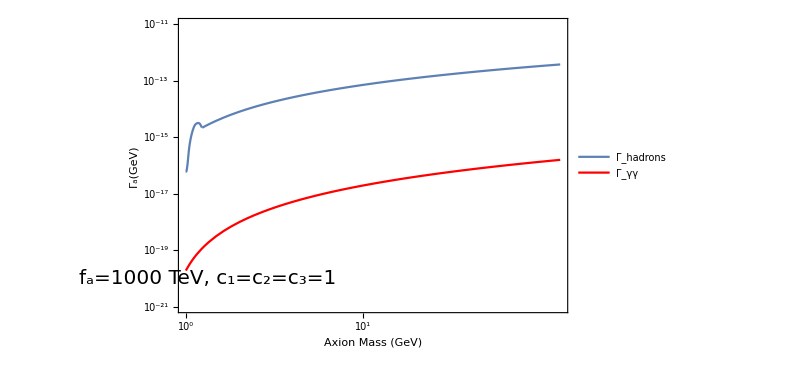

```mathematica
Show[LogPlot[Widthfunc[ma],{ma,1,20},PlotLegends->Placed[{Style["Γ_hadrons",FontSize->20,Black]},{0.85,0.3}],PlotRange-> {{1,20},{10^-21,10^-11}},Frame->True,Epilog->Style[Text[Style["f_a=1000 TeV, c_1=c_2=c_3=1",{20,Black}],{Log[8],Log[10^-20]}],20],FrameTicks->{{LogTicks[10,10^-21,10^-12,TickLabelStep->3,ShowMinorTicks-> False],GeVtocm},{LogTicks[10,0.9,20],LogTicks[10,0.9,20,ShowTickLabels-> False]}}],LogPlot[GammaPhoton[ma,1000*1000],{ma,1.0,20},PlotLegends->Placed[{Style["Γ_γγ",FontSize->20,Black]},{0.85,0.4}],PlotRange-> {{1,20},{10^-21,10^-11}},Frame->True,PlotStyle->Red],FrameLabel->{{Style["Γ_a(GeV)",FontSize->20,Black],Style["Lifetime (cm)",FontSize->20,Black]},{Style["Axion Mass (GeV)",FontSize->20,Black],None}},FrameTicksStyle->Directive[Black,18,AbsoluteThickness[1]],ImageSize-> 600]
```

```mathematica
GammaaglugluNLO[10,1,246]/KggNLO[10]
```

5.38766×10^-7

## Lifetime-M_a plot updates from Soubhik

#### Copying width data from 1811.03474 Fig. 3 left panel

```mathematica
widthdata=Import[NotebookDirectory[]<>"/constraints/decay\ width.csv","Data"]; (* from MIT paper, below is the full data *)
```

```mathematica
widthdata
```

{{0.0766077,0.00122477},{0.0849566,0.0020662},{0.0974512,0.00341789},{0.108024,0.00524628},{0.115148,0.00938441},{0.122561,0.0145476},{0.132481,0.0259004},{0.134473,0.0554863},{0.134521,0.0886491},{0.134562,0.132463},{0.134699,0.505229},{0.136616,0.00696664},{0.136985,0.258697},{0.138909,0.00381413},{0.141013,0.0116266},{0.150629,0.00223274},{0.152574,0.00106881},{0.154834,0.00216205},{0.163423,0.00352812},{0.172002,0.00528209},{0.182716,0.00727172},{0.200954,0.0121109},{0.22302,0.0199658},{0.238014,0.0265717},{0.253228,0.0349929},{0.28688,0.0604603},{0.317936,0.0931829},{0.351009,0.153619},{0.383507,0.250171},{0.417155,0.413268},{0.43874,0.669817},{0.461759,1.0637},{0.479032,1.62166},{0.499206,3.35755},{0.513628,6.32021},{0.525191,13.3554},{0.528105,20.3609},{0.541103,42.8789},{0.546434,81.9131},{0.547427,245.42},{0.547532,680.753},{0.547582,1110.88},{0.549832,400.487},{0.549845,148.868},{0.56551,42.4437},{0.571157,16.6593},{0.585436,7.7245},{0.616944,3.59386},{0.642769,2.99093},{0.685844,3.08389},{0.726061,3.61838},{0.760527,3.9261},{0.794992,4.20242},{0.832343,5.18883},{0.855373,9.18743},{0.874107,18.0147},{0.884251,45.123},{0.887072,27.6516},{0.892937,90.9172},{0.89874,163.184},{0.90454,285.033},{0.914783,618.921},{0.924394,1321.27},{0.929173,2590.74},{0.934719,6250.99},{0.942788,14528.7},{0.945522,595714.},{0.945896,310075.},{0.946347,25171.},{0.946601,933238.},{0.946651,1.5229×10^6},{0.946702,2.48513×10^6},{0.946752,4.05534×10^6},{0.946798,6.35305×10^6},{0.947329,142799.},{0.949091,46805.},{0.949139,74937.6},{0.963414,15980.2},{0.986716,7850.61},{1.03408,6423.39},{1.07144,8994.58},{1.1117,15604.3},{1.14478,27348.7},{1.17785,44628.8},{1.21522,65763.6},{1.2497,88706.6},{1.28993,117636.},{1.32442,150785.},{1.35889,175123.},{1.39336,203389.},{1.42784,236218.},{1.46231,270638.},{1.52262,297676.},{1.58293,318627.},{1.61739,322991.},{1.65184,318627.},{1.67194,316467.},{1.71357,292026.},{1.76094,256306.},{1.79539,239453.},{1.82984,217704.},{1.86142,214762.},{1.89588,214762.},{1.92746,208998.},{1.97916,227667.},{2.01362,230661.},{2.04807,230661.},{2.07679,228319.},{2.12274,247028.},{2.1572,250276.},{2.19166,255436.},{2.22611,246057.},{2.25771,263375.},{2.29217,274345.},{2.32375,274345.},{2.35821,274345.},{2.39267,274345.},{2.44437,297676.},{2.47882,294654.},{2.51328,297676.},{2.54487,297676.},{2.57454,301753.},{2.62241,322991.},{2.65687,327414.},{2.68845,319712.},{2.72291,322991.},{2.75736,319712.},{2.79182,322991.},{2.82342,354052.},{2.85788,357683.},{2.88659,350458.},{2.92105,345723.}}

```mathematica
width=widthdata;
width[[All,2]]=widthdata[[All,2]]/(32 Pi^2)^2/10^9; (* width is now in units of GeV for Subscript[f, a]=TeV *)
```

#### Various input params

```mathematica
mu=2.2/1000;
md=4.7/1000;
ms=20*md;
mc=1.275;
mb=4.18;
mt = 172.4;

mPi=135/1000;
mEta=0.548;
mEtap=0.958;

mK=497/1000;
Mz=91.1876;
Mz=91.18;
GammaZ=2.495;
Mw=80.379;

GF=1.166 10^(-5);
ThetawatMz = ArcSin[Sqrt[0.231]];
v=Sqrt[1/(Sqrt[2]GF)];

g2atMz=2 Mz Cos[ThetawatMz]/v;
gpatMz = g2atMz Tan[ThetawatMz];
g1atMz=Sqrt[5/3]gpatMz;
alpha1atMz = g1atMz^2/4/Pi;
alpha2atMz = g2atMz^2/4/Pi;

b1=41/10;
b2=-19/6;

alpha1[μ_]:=1/(1/alpha1atMz-b1/(2Pi)Log[μ/Mz]);
alpha2[μ_]:=1/(1/alpha2atMz-b2/(2Pi)Log[μ/Mz]);
alphaEM[mu_]:=3/5alpha1[mu]alpha2[mu]/(alpha2[mu]+3/5alpha1[mu]);

LambdaQCD=0.48;
Nf[μ_]:=4(*using 4 quark flavors*)
beta0[μ_]=11-2/3Nf[μ];
beta1[μ_] = 102-38/3Nf[μ];
z[mu_]:=-beta0[mu]^2/E/beta1[mu](LambdaQCD^2/mu^2)^(beta0[mu]^2/beta1[mu]);

alphas[μ_]:=-4Pi beta0[μ]/beta1[μ]/ProductLog[-1,z[μ]];(* using the expression in 1604.08082v3 eq. 3.21 *)
nflav=3;
EA=(97/4-7/6nflav);
KggNNLO[ma_,c3_,fa_]:=1+alphas[ma]/Pi EA+(alphas[ma]/Pi)^2EA(3/4 EA+(51/8-19/24nflav)/(11/4-nflav/6));
KggNLO[ma_]:=1+alphas[ma]/Pi EA;
GammaaglugluNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNLO[ma];
GammaaglugluNNLO[ma_,c3_,fa_]:=1/(32Pi^3)alphas[ma]^2ma^3/fa^2c3^2KggNNLO[ma,c3,fa];
(*This is in GeV*)
LifetimeinmmNLO[ma_,c3_,fa_]:=1/GammaaglugluNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
LifetimeinmmNNLO[ma_,c3_,fa_]:=1/GammaaglugluNNLO[ma,c3,fa]*0.198*10^(-12);(*this is in mm*)
```

#### Details of mixing

```mathematica
c2=1;c1=1;
c3=1;
cgamma[ma_]:=2c3((4+mu/md)/(3+3mu/md)-1/2*ma^2/(ma^2-mPi^2)*(1-mu/md)/(1+mu/md));
GammaPhoton[ma_,fa_]:=alphaEM[ma]^2/(256 Pi^3)cgamma[ma]^2 ma^3/fa^2;
LifetimePhoton[ma_,fa_]:=1/GammaPhoton[ma,fa]*0.198*10^(-15); (*in meter*)
fpi=0.093; (* differs from FASER value of fpi = 0.130 *)

(*mixingAPi[ma_,fa_]:=(1/6)ma^2/(ma^2-mPi^2)fpi/fa;
mixingAEta[ma_,fa_]:=(ma^2/Sqrt[6]-Sqrt[2/3] mPi^2/9)1/(ma^2-mEta^2)fpi/fa;
mixingAEtap[ma_,fa_]:=(ma^2/(2Sqrt[3])-4Sqrt[1/3] mPi^2/9)1/(ma^2-mEtap^2)fpi/fa;*)
mixingAPi[ma_,fa_]:=((1-mu/md)/(1+mu/md))fpi/(2fa)ma^2/(ma^2-mPi^2);
mixingAEta[ma_,fa_]:=(0.6)fpi/(2fa)ma^2/(ma^2-mEta^2);
mixingAEtap[ma_,fa_]:=(0.8)fpi/(2fa)ma^2/(ma^2-mEtap^2);

NPOT=1.47*10^22;
Naxions[ma_,fa_,seleff_]:=NPOT*(2.89*mixingAPi[ma,fa]^2+0.33*mixingAEta[ma,fa]^2+0.03*mixingAEtap[ma,fa]^2)*seleff;
```

```mathematica
LifetimePhoton[0.1,1/(4 Pi^2)]//ScientificForm
```

2.9241×10^-9

#### Numerical width function and comparison with a > γγ

InterpolatingFunction::dmval: Input value {0.015061} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

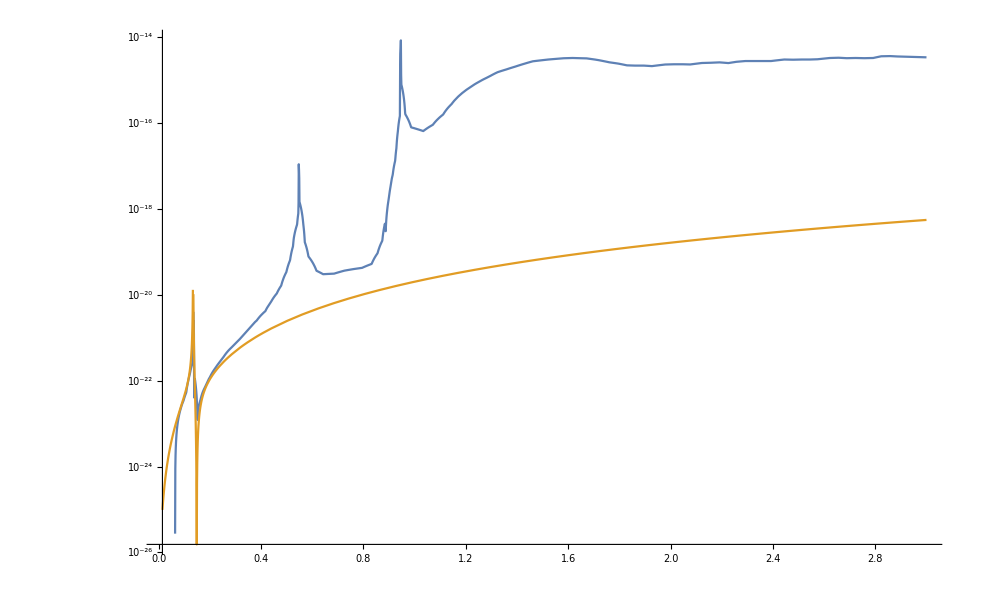

```mathematica
(*Change to unit of PeV----Zhen*)
WidthFunc=Interpolation[{#[[1]],#[[2]]/1000^2}&/@width,InterpolationOrder->1];
LogPlot[{WidthFunc[ma],GammaPhoton[ma,1000]/1000^2},{ma,0.015,3}]
```

## Cross section

```mathematica
xsinputs=Import[NotebookDirectory[]<>"cross_section//BeamdumpCrossSections.xlsx","XLSX"];
```

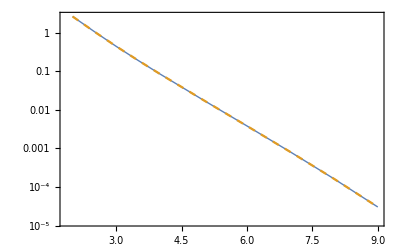

```mathematica
ListLogPlot[{{#[[1]],#[[2]]}&/@xsinputs[[1]],{#[[1]],#[[3]]}&/@xsinputs[[1]]},Joined->True,Frame->True,PlotStyle->{Thick,Dashed}]
```

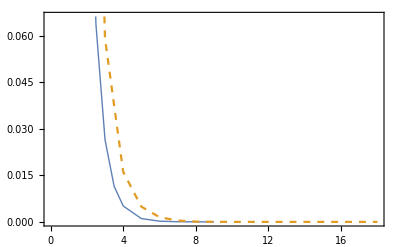

```mathematica
ListPlot[{{#[[1]],#[[2]](246/1000)^2}&/@xsinputs[[1]],{#[[1]],#[[3]](246/1000)^2*#[[4]]}&/@xsinputs[[2]]},Joined->True,Frame->True,PlotStyle->{Thick,Dashed}]
```

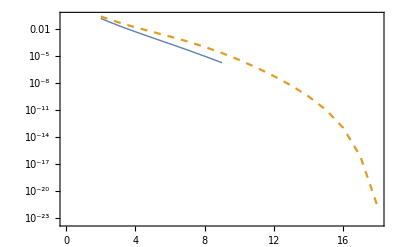

```mathematica
ListLogPlot[{{#[[1]],#[[2]](246/1000)^2}&/@xsinputs[[1]],{#[[1]],#[[3]](246/1000)^2*#[[4]]}&/@xsinputs[[2]]},Joined->True,Frame->True,PlotStyle->{Thick,Dashed}]
```

## Rate at DUNE ND

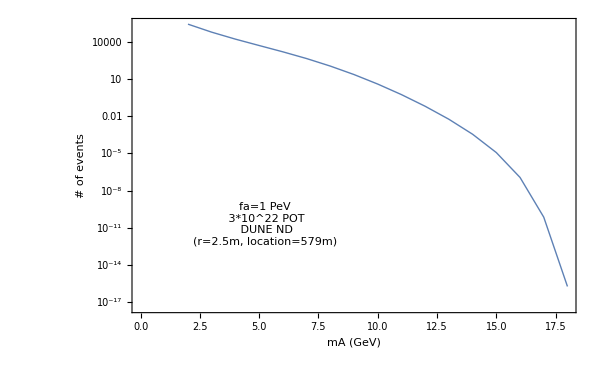

```mathematica
kfactor=3.0;
ListLogPlot[{{#[[1]],kfactor*#[[3]](246/1000000)^2 pb*#[[4]]*300*10^20 POT/(80*10^9 pb*POT)}&/@xsinputs[[2]]},Joined->True,Frame->True,PlotStyle->{Thick,Dashed},ImageSize->600,BaseStyle->16,FrameLabel->{"mA (GeV)","# of events"},Epilog->{Inset["fa=1 PeV\n 3*10^22 POT\n DUNE ND\n(r=2.5m, location=579m)",Scaled[{0.3,0.3}]]}]
```

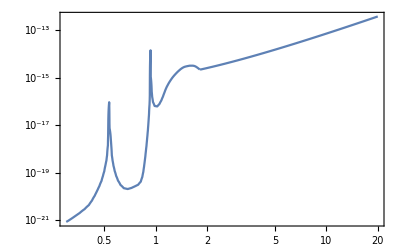

```mathematica
LogLogPlot[Widthfunc[ma],{ma,0.3,20},Frame->True]
```

```mathematica
decayprobability[τ_,distance_,decaylength_]:=Quiet[ⅇ^(-(decaylength+distance)/τ) (-1+ⅇ^(decaylength/τ))]
```

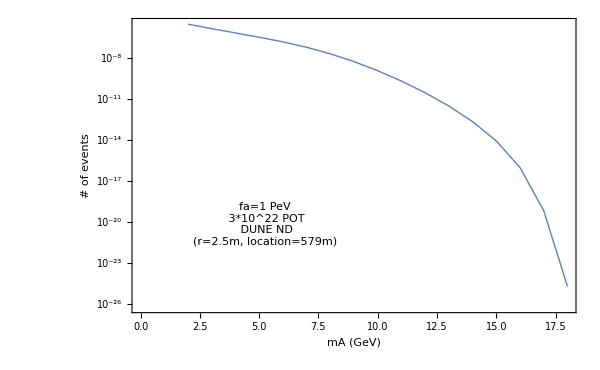

```mathematica
kfactor=3.0;
averageboostfactor=6.0;
InverseEVtoMeter=0.2*10^-6;
ListLogPlot[{{#[[1]],kfactor*#[[3]](246/1000000000)^2 pb*#[[4]]*300*10^20 POT/(80*10^9 pb*POT)*decayprobability[InverseEVtoMeter*10^6/(Widthfunc[#[[1]]]*10^9)*averageboostfactor,579,2.5*2]}&/@xsinputs[[2]]},Joined->True,Frame->True,PlotStyle->{Thick,Dashed},ImageSize->600,BaseStyle->16,FrameLabel->{"mA (GeV)","# of events"},Epilog->{Inset["fa=1 PeV\n 3*10^22 POT\n DUNE ND\n(r=2.5m, location=579m)",Scaled[{0.3,0.3}]]}]
```

```mathematica
observablerate[faPeV_,mass_,rate_]:=kfactor*rate(246/1000000/faPeV)^2 *300*10^20/(80*10^9)*decayprobability[InverseEVtoMeter*faPeV^2/(Widthfunc[mass]*10^9)*averageboostfactor,579,2.5*2]
observableratesimplify[faPeV_,mass_,rate_]:=kfactor*rate(246/1000000/faPeV)^2 *300*10^20/(80*10^9)*Exp[-579/(InverseEVtoMeter*faPeV^2/(Widthfunc[mass]*10^9)*averageboostfactor)]
```

```mathematica
simplifylist=observableratesimplify[faPeV,#[[1]],#[[3]]*#[[4]]]&/@xsinputs[[2]];
```

```mathematica
Maximize[observableratesimplify[faPeV,#[[1]],#[[3]]*#[[4]]],faPeV]&/@xsinputs[[2]][[1;;4]]
```

{{89.5834,{faPeV→-34.9016}},{9.65252,{faPeV→-50.368}},{1.48002,{faPeV→-67.2032}},{0.281502,{faPeV→-85.0528}}}

```mathematica
NSolve[observableratesimplify[faPeV,#[[1]],#[[3]]*#[[4]]]==3,faPeV,Reals]&/@xsinputs[[2]][[1;;4]]
```

{{{faPeV→-312.491},{faPeV→-13.9885},{faPeV→13.9885},{faPeV→312.491}},{{faPeV→-139.566},{faPeV→-27.3594},{faPeV→27.3594},{faPeV→139.566}},{},{}}

```mathematica
{#[[1]],Maximize[observablerate[faPeV,#[[1]],#[[3]]*#[[4]]],faPeV]}&/@xsinputs[[2]][[1;;4]]
{#[[1]],#[[2,1]],#[[2,2,1]],InverseEVtoMeter*faPeV^2/(Widthfunc[#[[1]]]*10^9)*averageboostfactor/.#[[2,2,1]]}&/@%
```

{{2.,{1.12862,{faPeV→-24.7322}}},{3.,{0.121608,{faPeV→-35.6922}}},{4.,{0.0186461,{faPeV→-47.622}}},{5.,{0.00354651,{faPeV→-60.2707}}}}

{{2.,1.12862,faPeV→-24.7322,290.746},{3.,0.121608,faPeV→-35.6922,290.746},{4.,0.0186461,faPeV→-47.622,290.746},{5.,0.00354651,faPeV→-60.2707,290.746}}

Above result indicates that gluonic production are lack of rate for sensitivities for ALPs with  a decay pipe at 579 down the beam.

```mathematica
{#[[1]],Maximize[observableratesimplify[faPeV,#[[1]],#[[3]]*#[[4]]],faPeV]}&/@xsinputs[[2]][[1;;4]]
{#[[1]],#[[2,1]],#[[2,2,1]],InverseEVtoMeter*faPeV^2/(Widthfunc[#[[1]]]*10^9)*averageboostfactor/.#[[2,2,1]]}&/@%
```

{{2.,{89.5834,{faPeV→-34.9016}}},{3.,{9.65252,{faPeV→-50.368}}},{4.,{1.48002,{faPeV→-67.2032}}},{5.,{0.281502,{faPeV→-85.0528}}}}

{{2.,89.5834,faPeV→-34.9016,579.},{3.,9.65252,faPeV→-50.368,579.},{4.,1.48002,faPeV→-67.2032,579.},{5.,0.281502,faPeV→-85.0528,579.}}

## Another attempt using gluon PDF

```mathematica
protonmass=0.938;
teamenergy=120;
comsquared=(teamenergy+protonmass)^2-(teamenergy^2-protonmass^2);
Sqrt[%]
```

15.0625

Changed my definition to 1/xx by following the equation in the middle of page 159 of Vernon’s Collider Physics book

```mathematica
ggpdf=Table[{rs,NIntegrate[xPDFcv[xx,rs^2,0]xPDFcv[rs^2/comsquared/xx,rs^2,0]/xx,{xx,rs^2/comsquared,1}],NIntegrate[xPDFcv[xx,rs^2/2,0]xPDFcv[rs^2/comsquared/xx,rs^2/2,0]/xx,{xx,rs^2/comsquared,1}],NIntegrate[xPDFcv[xx,2rs^2,0]xPDFcv[rs^2/comsquared/xx,2rs^2,0]/xx,{xx,rs^2/comsquared,1}]},{rs,0.3,Sqrt[comsquared],0.1}];
```

```mathematica
Export[NotebookDirectory[]<>"NNPDF_lo_as130_ggF_DUNE.m",ggpdf];
```

```mathematica
ggpdf[[1]]
```

{0.3,-5.13499,-1.39992×10^-15,-16.7533}

```mathematica
ggpdf=Import[NotebookDirectory[]<>"NNPDF_lo_as130_ggF_DUNE.m"];
```

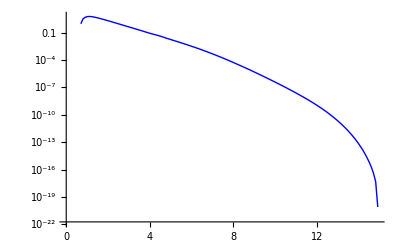

```mathematica
ListLogPlot[{#[[1]],#[[2]]}&/@ggpdf,Joined->True,PlotStyle->{Blue,Thick}]
```

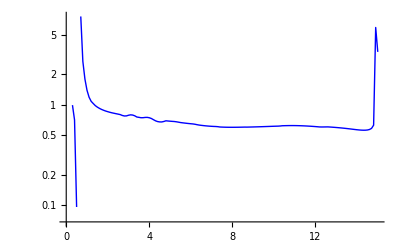

```mathematica
ListLogPlot[{#[[1]],#[[4]]/#[[2]]}&/@ggpdf,Joined->True,PlotStyle->{Blue,Thick}]
```

```mathematica
(*for the case of zero pT*)
Solve[y==1/2Log[(γ+Sqrt[γ^2-1])/(γ-Sqrt[γ^2-1])],γ]
rapiditytogamma[y_]:=1/2Sqrt[2+Exp[-2y]+Exp[2y]]
```

{{γ→-1/2 √(2+ⅇ^(-2 y)+ⅇ^(2 y))},{γ→1/2 √(2+ⅇ^(-2 y)+ⅇ^(2 y))}}

```mathematica
?alphas
```

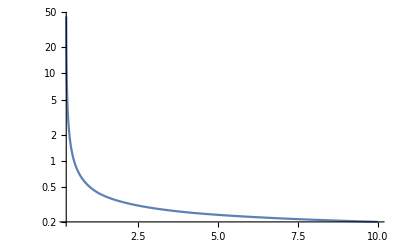

```mathematica
LogPlot[alphas[x^2,0,0][[1,1]],{x,0.25,10},PlotRange->Full]
```

converting width to parton level rate

```mathematica
decaygluon[x_]:=alphas[x^2,0,0][[1,1]]^2/(32Pi^3) x^3/(1000000)^2
partonrate[x_]:=1/(1/(2x)1/(16Pi)*8)*1/(2x^2)/(8*8*2*2)*(8)*2Pi/x^2 decaygluon[x]
```

```mathematica
1/(1/(2x)1/(16Pi)*8)*1/(2x^2)/(8*8*2*2)*(8)*2Pi/x^2
```

π^2/(8 x^3)

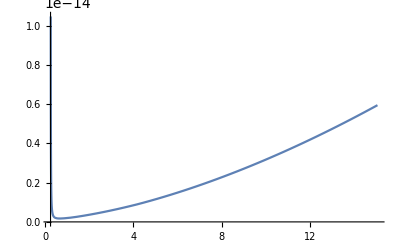

```mathematica
Plot[partonrate[x],{x,0.25,Sqrt[comsquared]}]
```

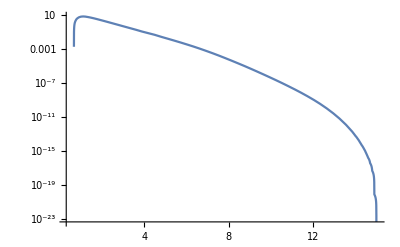

```mathematica
ggsfunc[x_]:=Interpolation[{#[[1]],#[[2]]}&/@ggpdf,InterpolationOrder->1][x]//Quiet
LogPlot[ggsfunc[x],{x,0.3,Sqrt[comsquared]}]
```

```mathematica
conversion=0.3894*10^9;(*from GeV^-2 to pb*)
```

```mathematica
colliderrate[x_]:=partonrate[x] ggsfunc[x]
```

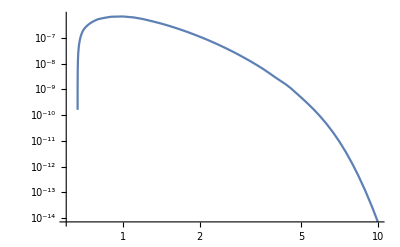

```mathematica
LogLogPlot[conversion*colliderrate[x],{x,0.6,10}]
```

```mathematica
Table[{x,conversion*colliderrate[x]*(10^6)^2*1.47*10^22*10^-42*10^6},{x,0.8,10,0.1}]
```

{{0.8,7.80508×10^-9},{0.9,9.71698×10^-9},{1.,9.97626×10^-9},{1.1,9.19802×10^-9},{1.2,7.91842×10^-9},{1.3,6.54326×10^-9},{1.4,5.43564×10^-9},{1.5,4.46764×10^-9},{1.6,3.66073×10^-9},{1.7,2.99603×10^-9},{1.8,2.4519×10^-9},{1.9,2.00782×10^-9},{2.,1.64639×10^-9},{2.1,1.35158×10^-9},{2.2,1.1115×10^-9},{2.3,9.15743×10^-10},{2.4,7.55312×10^-10},{2.5,6.24623×10^-10},{2.6,5.16843×10^-10},{2.7,4.28276×10^-10},{2.8,3.55748×10^-10},{2.9,2.9568×10^-10},{3.,2.45927×10^-10},{3.1,2.04932×10^-10},{3.2,1.71195×10^-10},{3.3,1.42846×10^-10},{3.4,1.19327×10^-10},{3.5,9.98297×10^-11},{3.6,8.36782×10^-11},{3.7,6.96075×10^-11},{3.8,5.76749×10^-11},{3.9,4.80877×10^-11},{4.,4.04066×10^-11},{4.1,3.42714×10^-11},{4.2,2.93854×10^-11},{4.3,2.52054×10^-11},{4.4,2.14605×10^-11},{4.5,1.81145×10^-11},{4.6,1.51367×10^-11},{4.7,1.25×10^-11},{4.8,1.0273×10^-11},{4.9,8.61539×10^-12},{5.,7.22267×10^-12},{5.1,6.05332×10^-12},{5.2,5.07218×10^-12},{5.3,4.24954×10^-12},{5.4,3.56031×10^-12},{5.5,2.9817×10^-12},{5.6,2.48642×10^-12},{5.7,2.07056×10^-12},{5.8,1.72182×10^-12},{5.9,1.42978×10^-12},{6.,1.1856×10^-12},{6.1,9.81774×10^-13},{6.2,8.11938×10^-13},{6.3,6.70693×10^-13},{6.4,5.51941×10^-13},{6.5,4.52053×10^-13},{6.6,3.69274×10^-13},{6.7,3.00876×10^-13},{6.8,2.44532×10^-13},{6.9,1.98262×10^-13},{7.,1.60385×10^-13},{7.1,1.29474×10^-13},{7.2,1.04324×10^-13},{7.3,8.39229×10^-14},{7.4,6.74005×10^-14},{7.5,5.37533×10^-14},{7.6,4.2767×10^-14},{7.7,3.39504×10^-14},{7.8,2.68958×10^-14},{7.9,2.12673×10^-14},{8.,1.67883×10^-14},{8.1,1.32323×10^-14},{8.2,1.04153×10^-14},{8.3,8.18814×10^-15},{8.4,6.43059×10^-15},{8.5,5.04581×10^-15},{8.6,3.95633×10^-15},{8.7,3.09619×10^-15},{8.8,2.40972×10^-15},{8.9,1.87253×10^-15},{9.,1.45288×10^-15},{9.1,1.12558×10^-15},{9.2,8.70712×10^-16},{9.3,6.72549×10^-16},{9.4,5.18715×10^-16},{9.5,3.99484×10^-16},{9.6,3.0722×10^-16},{9.7,2.35938×10^-16},{9.8,1.80956×10^-16},{9.9,1.38613×10^-16},{10.,1.06053×10^-16}}

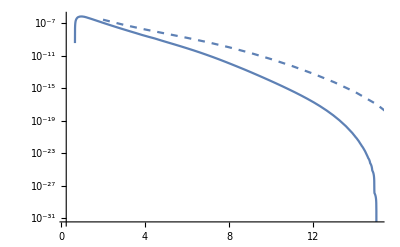

```mathematica
Show[Quiet[LogPlot[conversion*colliderrate[x],{x,0.25,Sqrt[comsquared]}]],ListLogPlot[{{#[[1]],#[[3]](246/1000000)^2}&/@xsinputs[[2]]},Joined->True,Frame->True,PlotStyle->{Dashed}]]
```

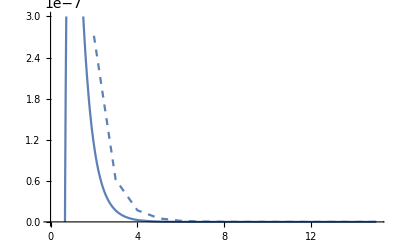

```mathematica
Show[Quiet[Plot[conversion*colliderrate[x],{x,0.25,Sqrt[comsquared]},PlotRange->{0,3*10^-7}]],ListPlot[{{#[[1]],#[[3]](246/1000000)^2}&/@xsinputs[[2]]},Joined->True,PlotRange->Full,Frame->True,PlotStyle->{Dashed}]]
```

With scale variation

```mathematica
decaygluon[x_,scale_]:=alphas[x^2 scale,0,0][[1,1]]^2/(32Pi^3) x^3/(1000000)^2
partonrate[x_,scale_]:=1/(1/(2x)1/(16Pi)*8)*1/(2x^2)/(8*8*2*2)*(8)*2Pi/x^2 decaygluon[x,scale]
ggsfunc[x_,choice_]:=Interpolation[{#[[1]],If[choice==2,#[[3]],If[choice==3,#[[4]],#[[2]]]]}&/@ggpdf,InterpolationOrder->1][x]//Quiet
colliderrate[x_,choice_]:=partonrate[x,If[choice==2,1/2,If[choice==3,2,1]]] ggsfunc[x,choice]
```

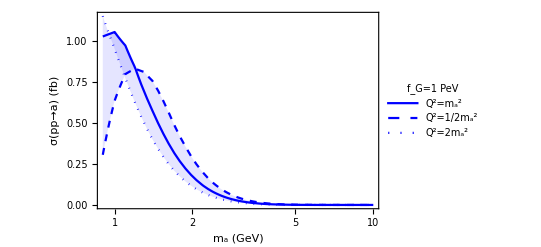

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
LogLinearPlot[{conversion*colliderrate[x,1]*10^3*(4Pi^2)^2,conversion*colliderrate[x,2]*10^3*(4Pi^2)^2,conversion*colliderrate[x,3]*10^3*(4Pi^2)^2},{x,0.9,10},Filling->{3->{1},2->{1}},FillingStyle->{Directive[Blue,Opacity[0.1]]},PlotStyle->{Blue,{Blue,Dashed},{Blue,Dotted}},PlotRange->{0,Automatic},ImageSize->400,Frame->True,BaseStyle->14,FrameLabel->{{"σ(pp→a) (fb)",""},{"m_a (GeV)","120 GeV Proton Beam Energy"}},PlotLegends->Placed[LineLegend[Style[#,12]&/@{"Q^2=m_a^2","Q^2=1/2m_a^2","Q^2=2m_a^2"},LegendFunction->frame,LegendLabel->Style["f_G=1 PeV",16]],Scaled[{0.8,0.7}]]]
```

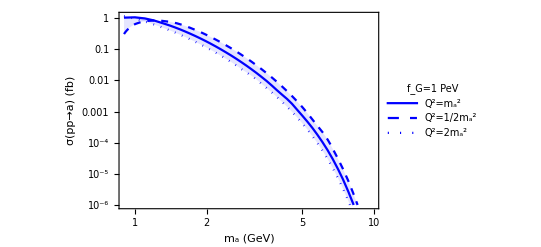

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
LogLogPlot[{conversion*If[colliderrate[x,1]>0,colliderrate[x,1],10^-30]*10^3*(4Pi^2)^2,conversion*If[colliderrate[x,2]>0,colliderrate[x,2],10^-30]*10^3*(4Pi^2)^2,conversion*colliderrate[x,3]*10^3*(4Pi^2)^2},{x,0.9,10},Filling->{3->{1},2->{1}},FillingStyle->{Directive[Blue,Opacity[0.1]]},PlotStyle->{Blue,{Blue,Dashed},{Blue,Dotted}},PlotRange->{10^-6,Automatic},ImageSize->400,Frame->True,BaseStyle->14,FrameLabel->{{"σ(pp→a) (fb)",""},{"m_a (GeV)","120 GeV Proton Beam Energy"}},PlotLegends->Placed[LineLegend[Style[#,12]&/@{"Q^2=m_a^2","Q^2=1/2m_a^2","Q^2=2m_a^2"},LegendFunction->frame,LegendLabel->Style["f_G=1 PeV",16]],Scaled[{0.22,0.35}]],FrameTicks->{{LogTicks[10,10^-8,10^-0,TickLabelStep->2,ShowMinorTicks-> False],StripTickLabels[LogTicks[10,10^-8,10^-0,TickLabelStep->2,ShowMinorTicks-> False]]},{Automatic,Automatic}}]
```

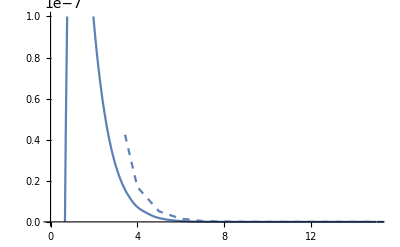

```mathematica
Show[Quiet[Plot[conversion*colliderrate[x],{x,0.25,Sqrt[comsquared]},PlotRange->{0,10^-7}]],ListPlot[{{#[[1]],#[[3]](246/1000000)^2}&/@xsinputs[[2]]},Joined->True,Frame->True,PlotStyle->{Dashed}]]
```

```mathematica
inputs=Table[{x,colliderrate[x]},{x,0.8,5,0.1}]
```

{{0.8,3.29047×10^-16},{0.9,4.7136×10^-16},{1.,5.52551×10^-16},{1.1,5.77188×10^-16},{1.2,5.58862×10^-16},{1.3,5.1636×10^-16},{1.4,4.77767×10^-16},{1.5,4.34745×10^-16},{1.6,3.92248×10^-16},{1.7,3.51763×10^-16},{1.8,3.14044×10^-16},{1.9,2.79411×10^-16},{2.,2.48018×10^-16},{2.1,2.19663×10^-16},{2.2,1.94287×10^-16},{2.3,1.71665×10^-16},{2.4,1.51446×10^-16},{2.5,1.33632×10^-16},{2.6,1.17712×10^-16},{2.7,1.03617×10^-16},{2.8,9.12494×10^-17},{2.9,8.0257×10^-17},{3.,7.05153×10^-17},{3.1,6.19716×10^-17},{3.2,5.45139×10^-17},{3.3,4.78282×10^-17},{3.4,4.19522×10^-17},{3.5,3.68055×10^-17},{3.6,3.23121×10^-17},{3.7,2.8119×10^-17},{3.8,2.43466×10^-17},{3.9,2.11901×10^-17},{4.,1.85677×10^-17},{4.1,1.6407×10^-17},{4.2,1.46445×10^-17},{4.3,1.30713×10^-17},{4.4,1.1571×10^-17},{4.5,1.01463×10^-17},{4.6,8.80065×10^-18},{4.7,7.53819×10^-18},{4.8,6.42114×10^-18},{4.9,5.57753×10^-18},{5.,4.83977×10^-18}}

```mathematica
observableratenew[faPeV_,mass_,rate_,averageboostfactor_]:=kfactor*rate(1/faPeV)^2 *300*10^20/(80*10^9)*decayprobability[InverseEVtoMeter*faPeV^2/(Widthfunc[mass]*10^9)*averageboostfactor,579,2.5*2*2]
observableratesimplifynew[faPeV_,mass_,rate_]:=kfactor*rate(1/faPeV)^2 *300*10^20/(80*10^9)*Exp[-579/(InverseEVtoMeter*faPeV^2/(Widthfunc[mass]*10^9)*averageboostfactor)]
```

```mathematica
Log[(teamenergy+protonmass+Sqrt[teamenergy^2-protonmass^2])/(teamenergy+protonmass-Sqrt[teamenergy^2-protonmass^2])]
```

5.54463

```mathematica
E^5.5
```

244.692

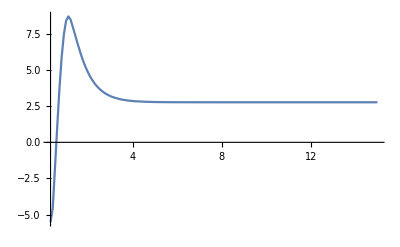

{{0.8,{2.42835×10^6,{faPeV→0.0165867}}},{0.9,{112560.,{faPeV→0.092209}}},{1.,{27777.8,{faPeV→-0.200967}}},{1.1,{16531.1,{faPeV→-0.266254}}},{1.2,{3104.89,{faPeV→0.604529}}},{1.3,{787.844,{faPeV→-1.15357}}},{1.4,{259.076,{faPeV→-1.93501}}},{1.5,{104.881,{faPeV→-2.90107}}},{1.6,{51.7789,{faPeV→-3.92187}}},{1.7,{30.2642,{faPeV→-4.8579}}},{1.8,{23.1662,{faPeV→5.24634}}},{1.9,{14.0147,{faPeV→-6.36235}}},{2.,{8.2152,{faPeV→-7.82926}}},{2.1,{5.02622,{faPeV→9.4199}}},{2.2,{3.20106,{faPeV→11.101}}},{2.3,{2.11298,{faPeV→-12.8434}}},{2.4,{1.43738,{faPeV→14.6262}}},{2.5,{1.00698,{faPeV→-16.4147}}},{2.6,{0.721087,{faPeV→-18.2056}}},{2.7,{0.527162,{faPeV→-19.977}}}}

{{0.8,2.42835×10^6,faPeV→0.0165867,291.986},{0.9,112560.,faPeV→0.092209,291.986},{1.,27777.8,faPeV→-0.200967,291.986},{1.1,16531.1,faPeV→-0.266254,291.986},{1.2,3104.89,faPeV→0.604529,291.986},{1.3,787.844,faPeV→-1.15357,291.986},{1.4,259.076,faPeV→-1.93501,291.986},{1.5,104.881,faPeV→-2.90107,291.986},{1.6,51.7789,faPeV→-3.92187,291.986},{1.7,30.2642,faPeV→-4.8579,291.986},{1.8,23.1662,faPeV→5.24634,291.986},{1.9,14.0147,faPeV→-6.36235,291.986},{2.,8.2152,faPeV→-7.82926,291.986},{2.1,5.02622,faPeV→9.4199,291.986},{2.2,3.20106,faPeV→11.101,291.986},{2.3,2.11298,faPeV→-12.8434,291.986},{2.4,1.43738,faPeV→14.6262,291.986},{2.5,1.00698,faPeV→-16.4147,291.986},{2.6,0.721087,faPeV→-18.2056,291.986},{2.7,0.527162,faPeV→-19.977,291.986}}

```mathematica
Plot[averageboostfactorfunc[x],{x,0.3,15},PlotRange->Full]
{#[[1]],Maximize[observableratenew[faPeV,#[[1]],conversion#[[2]],rapiditytogamma[averageboostfactorfunc[#[[1]]]]],faPeV]}&/@inputs[[1;;20]]
optimalpointslist={#[[1]],#[[2,1]],#[[2,2,1]],InverseEVtoMeter*faPeV^2/(Widthfunc[#[[1]]]*10^9)*rapiditytogamma[averageboostfactorfunc[#[[1]]]]/.#[[2,2,1]]}&/@%
```

```mathematica
limitsolutions={#[[1]],NSolve[observableratenew[faPeV,#[[1]],conversion#[[2]],rapiditytogamma[averageboostfactorfunc[#[[1]]]]]==3,faPeV,Reals]}&/@inputs[[1;;20]]
```

{{0.8,{{faPeV→-0.820111},{faPeV→-0.0052144},{faPeV→0.0052144},{faPeV→0.820111}}},{0.9,{{faPeV→-2.11387},{faPeV→-0.031824},{faPeV→0.031824},{faPeV→2.11387}}},{1.,{{faPeV→-3.24406},{faPeV→-0.0729211},{faPeV→0.0729211},{faPeV→3.24406}}},{1.1,{{faPeV→-3.77279},{faPeV→-0.0985761},{faPeV→0.0985761},{faPeV→3.77279}}},{1.2,{{faPeV→-5.62068},{faPeV→-0.240571},{faPeV→0.240571},{faPeV→5.62068}}},{1.3,{{faPeV→-7.56801},{faPeV→-0.4924},{faPeV→0.4924},{faPeV→7.56801}}},{1.4,{{faPeV→-9.52694},{faPeV→-0.883414},{faPeV→0.883414},{faPeV→9.52694}}},{1.5,{{faPeV→-11.2503},{faPeV→-1.41283},{faPeV→1.41283},{faPeV→11.2503}}},{1.6,{{faPeV→-12.5517},{faPeV→-2.02667},{faPeV→2.02667},{faPeV→12.5517}}},{1.7,{{faPeV→-13.3613},{faPeV→-2.64586},{faPeV→2.64586},{faPeV→13.3613}}},{1.8,{{faPeV→-13.3472},{faPeV→-2.94265},{faPeV→2.94265},{faPeV→13.3472}}},{1.9,{{faPeV→-13.8848},{faPeV→-3.80176},{faPeV→3.80176},{faPeV→13.8848}}},{2.,{{faPeV→-14.2914},{faPeV→-5.09194},{faPeV→5.09194},{faPeV→14.2914}}},{2.1,{{faPeV→-14.1637},{faPeV→-6.83429},{faPeV→6.83429},{faPeV→14.1637}}},{2.2,{{faPeV→-12.6801},{faPeV→-9.82444},{faPeV→9.82444},{faPeV→12.6801}}},{2.3,{}},{2.4,{}},{2.5,{}},{2.6,{}},{2.7,{}}}

{{0.8,0.820111},{0.9,2.11387},{1.,3.24406},{1.1,3.77279},{1.2,5.62068},{1.3,7.56801},{1.4,9.52694},{1.5,11.2503},{1.6,12.5517},{1.7,13.3613},{1.8,13.3472},{1.9,13.8848},{2.,14.2914},{2.1,14.1637},{2.2,12.6801}}

{{0.8,0.0052144},{0.9,0.031824},{1.,0.0729211},{1.1,0.0985761},{1.2,0.240571},{1.3,0.4924},{1.4,0.883414},{1.5,1.41283},{1.6,2.02667},{1.7,2.64586},{1.8,2.94265},{1.9,3.80176},{2.,5.09194},{2.1,6.83429},{2.2,9.82444}}

{{0.8,0.0165867},{0.9,0.092209},{1.,0.200967},{1.1,0.266254},{1.2,0.604529},{1.3,1.15357},{1.4,1.93501},{1.5,2.90107},{1.6,3.92187},{1.7,4.8579},{1.8,5.24634},{1.9,6.36235},{2.,7.82926},{2.1,9.4199},{2.2,11.101}}

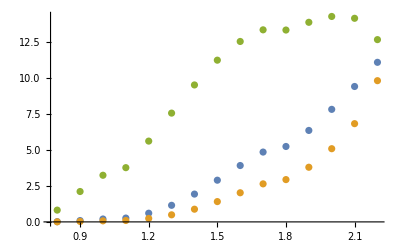

```mathematica
{#[[1]],Abs[#[[2,1,1,2]]]}&/@limitsolutions[[1;;15]]
{#[[1]],Abs[#[[2,2,1,2]]]}&/@limitsolutions[[1;;15]]
{#[[1]],Abs[#[[3,2]]]}&/@optimalpointslist[[1;;15]]
ListPlot[{%,%%,%%%}]
```

```mathematica
limitsolutions1event={#[[1]],NSolve[observableratenew[faPeV,#[[1]],conversion#[[2]],rapiditytogamma[averageboostfactorfunc[#[[1]]]]]==1,faPeV,Reals]}&/@inputs[[1;;20]]
```

{{0.8,{{faPeV→-1.07942},{faPeV→-0.00506448},{faPeV→0.00506448},{faPeV→1.07942}}},{0.9,{{faPeV→-2.78313},{faPeV→-0.0307087},{faPeV→0.0307087},{faPeV→2.78313}}},{1.,{{faPeV→-4.27289},{faPeV→-0.0700767},{faPeV→0.0700767},{faPeV→4.27289}}},{1.1,{{faPeV→-4.97051},{faPeV→-0.0945611},{faPeV→0.0945611},{faPeV→4.97051}}},{1.2,{{faPeV→-7.41546},{faPeV→-0.229119},{faPeV→0.229119},{faPeV→7.41546}}},{1.3,{{faPeV→-10.0097},{faPeV→-0.465086},{faPeV→0.465086},{faPeV→10.0097}}},{1.4,{{faPeV→-12.6506},{faPeV→-0.826581},{faPeV→0.826581},{faPeV→12.6506}}},{1.5,{{faPeV→-15.0241},{faPeV→-1.30789},{faPeV→1.30789},{faPeV→15.0241}}},{1.6,{{faPeV→-16.8836},{faPeV→-1.85466},{faPeV→1.85466},{faPeV→16.8836}}},{1.7,{{faPeV→-18.123},{faPeV→-2.3929},{faPeV→2.3929},{faPeV→18.123}}},{1.8,{{faPeV→-18.2049},{faPeV→-2.64184},{faPeV→2.64184},{faPeV→18.2049}}},{1.9,{{faPeV→-19.2134},{faPeV→-3.35251},{faPeV→3.35251},{faPeV→19.2134}}},{2.,{{faPeV→-20.2852},{faPeV→-4.36063},{faPeV→4.36063},{faPeV→20.2852}}},{2.1,{{faPeV→-21.0361},{faPeV→-5.57274},{faPeV→5.57274},{faPeV→21.0361}}},{2.2,{{faPeV→-21.3994},{faPeV→-7.0254},{faPeV→7.0254},{faPeV→21.3994}}},{2.3,{{faPeV→-21.2787},{faPeV→-8.79938},{faPeV→8.79938},{faPeV→21.2787}}},{2.4,{{faPeV→-20.4405},{faPeV→-11.1236},{faPeV→11.1236},{faPeV→20.4405}}},{2.5,{{faPeV→-17.1239},{faPeV→-15.753},{faPeV→15.753},{faPeV→17.1239}}},{2.6,{}},{2.7,{}}}

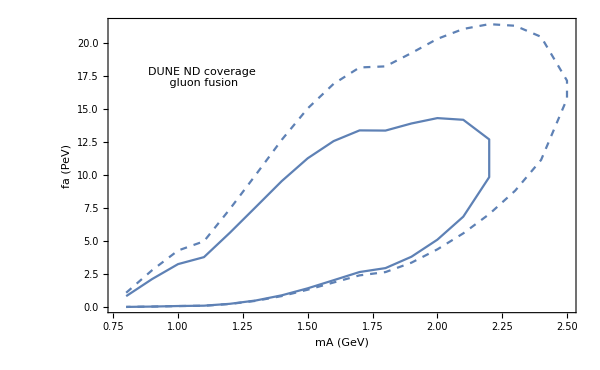

```mathematica
Show[
ListPlot[Flatten[{List[{#[[1]],Abs[faPeV]/.#[[2,1]]}&/@limitsolutions1event[[1;;18]]][[1]],ReverseSortBy[List[{#[[1]],Abs[faPeV]/.#[[2,2]]}&/@limitsolutions1event[[1;;18]]][[1]],1]},1],Joined->True,Frame->True,PlotStyle->Dashed,FrameLabel->{"mA (GeV)","fa (PeV)"},BaseStyle->16,ImageSize->600,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.2,0.8}]]],ListPlot[Flatten[{List[{#[[1]],Abs[faPeV]/.#[[2,1]]}&/@limitsolutions[[1;;15]]][[1]],ReverseSortBy[List[{#[[1]],Abs[faPeV]/.#[[2,2]]}&/@limitsolutions[[1;;15]]][[1]],1]},1],Joined->True,Frame->True,FrameLabel->{"mA (GeV)","fa (PeV)"},BaseStyle->16,ImageSize->600,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.2,0.8}]]]]
```

What’s the effective decay volume for such energetic particles?

r=2.5, d=5m+5m

## More detailed calculation (slower) with simulations and particle momentum spread

```mathematica
protonmass=0.938;
teamenergy=120;
comsquared=(teamenergy+protonmass)^2-(teamenergy^2-protonmass^2);
Sqrt[%]
conversion=0.3894*10^9;(*from GeV^-2 to pb*)
decaygluon[x_]:=alphas[x^2,0,0][[1,1]]^3/(32Pi^3) x^3/(1000000)^2
partonrate[x_]:=1/(1/(2x)1/(16Pi)*1/2*8)*1/(2x^2)/(8*8)*(1/2*8)decaygluon[x]
labframerap=1/2Log[(teamenergy+protonmass+Sqrt[teamenergy^2-protonmass^2])/(teamenergy+protonmass-Sqrt[teamenergy^2-protonmass^2])]
```

15.0625

2.77231

```mathematica
grandfunctionpermasspoint[mass_,detectorlength_,statistics_,faPeV_]:=
Module[{xx,eventrapidity,pdfweight,eventweight,components},
components=
Table[Total[Table[xx=RandomReal[{mass^2/comsquared,1}];
pdfweight=xPDFcv[xx,mass^2,0]xPDFcv[mass^2/comsquared/xx,mass^2,0]/xx;
eventrapidity=1/2Abs[Log[xx^2/(mass^2/comsquared)]];
{eventweight=pdfweight*partonrate[mass]*conversion*kfactor*(1/faPeV)^2 *300*10^20/(80*10^9)*decayprobability[InverseEVtoMeter*faPeV^2/(Widthfunc[mass]*10^9)*rapiditytogammabeta[eventrapidity+labframerap],579,detectorlength]/(1-mass^2/comsquared),eventrapidity},{i,1,statistics/10}]]/(statistics/10),{j,1,10}];
{mass,faPeV,Mean[#[[1]]&/@components],StandardDeviation[#[[1]]&/@components],detectorlength,Mean[#[[2]]&/@components],StandardDeviation[#[[2]]&/@components]}
];
```

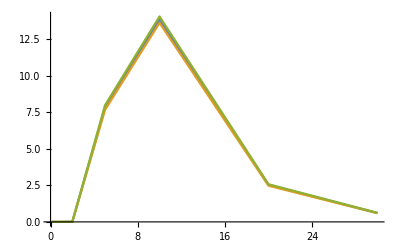

```mathematica
ListPlot[{{#[[2]],#[[3]]}&/@%131,{#[[2]],#[[3]]-#[[4]]}&/@%131,{#[[2]],#[[3]]+#[[4]]}&/@%131},Joined->True]
```

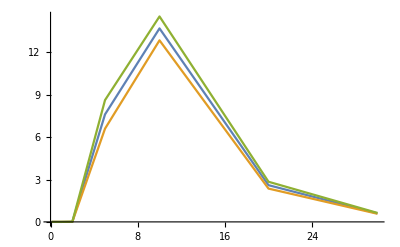

```mathematica
ListPlot[{{#[[2]],#[[3]]}&/@%136,{#[[2]],#[[3]]-#[[4]]}&/@%136,{#[[2]],#[[3]]+#[[4]]}&/@%136},Joined->True]
```

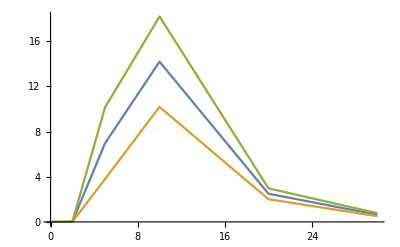

```mathematica
ListPlot[{{#[[2]],#[[3]]}&/@%138,{#[[2]],#[[3]]-#[[4]]}&/@%138,{#[[2]],#[[3]]+#[[4]]}&/@%138},Joined->True]
```

```mathematica
particularmasseff=Table[Quiet[grandfunctionpermasspoint[0.8,10,10^4,faPeV]],{faPeV,{1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50}}];
```

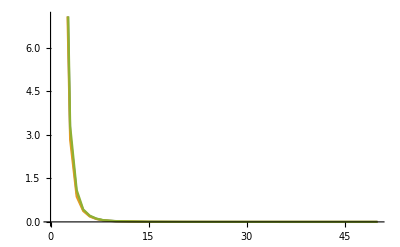

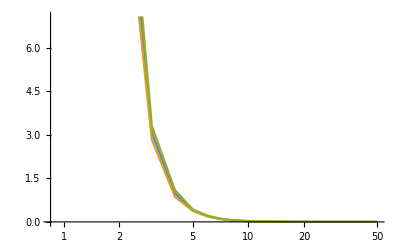

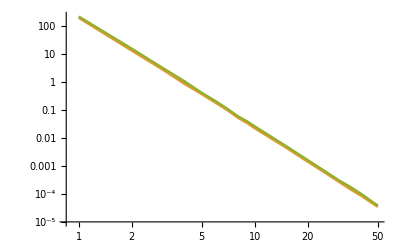

```mathematica
ListPlot[{{#[[2]],#[[3]]}&/@particularmasseff,{#[[2]],#[[3]]-#[[4]]}&/@particularmasseff,{#[[2]],#[[3]]+#[[4]]}&/@particularmasseff},Joined->True]
ListLogLinearPlot[{{#[[2]],#[[3]]}&/@particularmasseff,{#[[2]],#[[3]]-#[[4]]}&/@particularmasseff,{#[[2]],#[[3]]+#[[4]]}&/@particularmasseff},Joined->True]
ListLogLogPlot[{{#[[2]],#[[3]]}&/@particularmasseff,{#[[2]],#[[3]]-#[[4]]}&/@particularmasseff,{#[[2]],#[[3]]+#[[4]]}&/@particularmasseff},Joined->True]
```

```mathematica
simulationresults=Table[Table[Quiet[grandfunctionpermasspoint[masslist,10,10^3,faPeV]],{faPeV,{0.01,0.02,0.05,0.1,0.2,0.5,0.8,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50}}],{masslist,0.8,3.2,0.1}];
```

```mathematica
Export[NotebookDirectory[]<>"simulationresult.m",simulationresults]
```

C:\Users\novar\Dropbox\Axion@DUNEND\research\simulationresult.m

```mathematica
simulationresults=Import[NotebookDirectory[]<>"simulationresult.m"];
```

```mathematica
simulationresults[[1]]
```

{{0.8,0.01,6.9225×10^-9,2.18909×10^-8,10,2.03504,0.0950934},{0.8,0.02,955.743,2109.46,10,2.07953,0.0763303},{0.8,0.05,28887.6,30800.,10,2.06706,0.0611406},{0.8,0.1,21812.,15969.1,10,2.02569,0.0801635},{0.8,0.2,16598.2,4913.11,10,2.0268,0.102038},{0.8,0.5,1574.51,427.314,10,2.0775,0.0430698},{0.8,0.8,287.576,79.3144,10,2.02216,0.081585},{0.8,1,122.045,26.3075,10,1.99848,0.0854271},{0.8,2,8.89839,2.0458,10,2.03835,0.0941975},{0.8,3,1.66108,0.598063,10,2.04307,0.0594444},{0.8,4,0.475716,0.20605,10,2.0758,0.053597},{0.8,5,0.195297,0.0611658,10,2.06609,0.0850163},{0.8,6,0.0858104,0.029608,10,2.06016,0.0794154},{0.8,7,0.0539655,0.0139873,10,2.01658,0.0899744},{0.8,8,0.0374707,0.00607481,10,2.00707,0.0748519},{0.8,9,0.0187912,0.00465317,10,2.06847,0.0346217},{0.8,10,0.0127202,0.00219333,10,2.01336,0.0571964},{0.8,15,0.00310405,0.000790733,10,1.99653,0.0565027},{0.8,20,0.000744302,0.000249408,10,2.05939,0.0575395},{0.8,25,0.000355594,0.0000995074,10,2.02191,0.0519676},{0.8,30,0.000178432,0.0000769432,10,1.99389,0.104861},{0.8,35,0.0000991771,0.0000325567,10,2.01039,0.0771231},{0.8,40,0.0000488554,0.0000241683,10,2.09054,0.0886912},{0.8,50,0.0000210194,6.1534×10^-6,10,2.02878,0.0623143}}

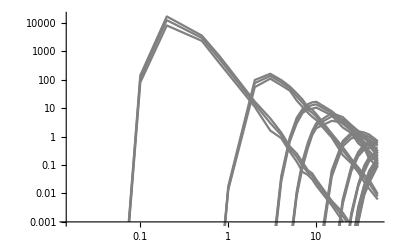

```mathematica
Show[
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[1]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[1]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[1]]},Joined->True,PlotRange->{10^-3,Full},PlotStyle->Gray],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[2]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[2]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[2]]},Joined->True,PlotRange->Full,PlotStyle->Gray],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[3]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[3]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[3]]},Joined->True,PlotRange->Full,PlotStyle->Gray],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[4]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[4]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[4]]},Joined->True,PlotRange->Full,PlotStyle->Gray],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[5]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[5]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[5]]},Joined->True,PlotRange->Full,PlotStyle->Gray],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[6]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[6]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[6]]},Joined->True,PlotRange->Full,PlotStyle->Gray],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[7]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[7]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[7]]},Joined->True,PlotRange->Full,PlotStyle->Gray],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[8]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[8]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[8]]},Joined->True,PlotRange->Full,PlotStyle->Gray],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[9]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[9]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[9]]},Joined->True,PlotRange->Full,PlotStyle->Gray]
]
```

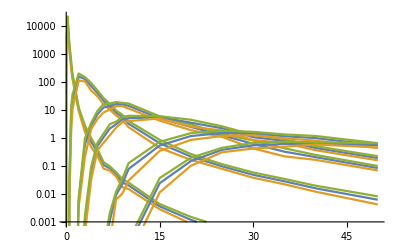

```mathematica
(*A seperate run's result*)
Show[
ListLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[1]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[1]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[1]]},Joined->True,PlotRange->{10^-3,Full}],
ListLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[2]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[2]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[2]]},Joined->True,PlotRange->Full],
ListLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[3]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[3]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[3]]},Joined->True,PlotRange->Full],
ListLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[4]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[4]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[4]]},Joined->True,PlotRange->Full],
ListLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[5]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[5]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[5]]},Joined->True,PlotRange->Full],
ListLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[6]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[6]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[6]]},Joined->True,PlotRange->Full]
]
```

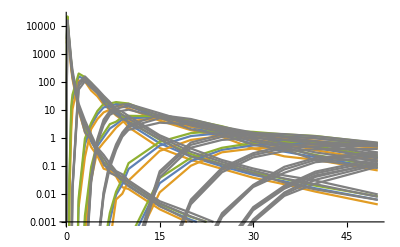

```mathematica
Show[%174,%203]
```

```mathematica
LogPlot[alphas[x^2,0,0][[1,1]],{x,0.25,10},PlotRange->Full]
```

-Graphics-

converting width to parton level rate

```mathematica
decaygluon[x_]:=alphas[x^2,0,0][[1,1]]^3/(32Pi^3) x^3/(1000000)^2
partonrate[x_]:=1/(1/(2x)1/(16Pi)*1/2*8)*1/(2x^2)/(8*8)*(1/2*8)decaygluon[x]
```

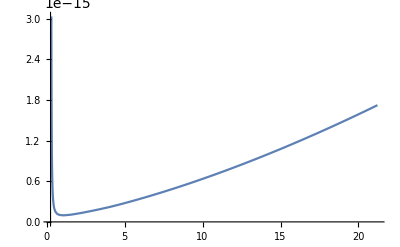

```mathematica
Plot[partonrate[x],{x,0.25,Sqrt[comsquared]}]
```

```mathematica
ggsfunc[x_]:=Interpolation[{#[[1]],#[[2]]}&/@ggpdf,InterpolationOrder->1][x]//Quiet
LogPlot[ggsfunc[x],{x,0.3,Sqrt[comsquared]}]
```

-Graphics-

```mathematica
conversion=0.3894*10^9;(*from GeV^-2 to pb*)
```

```mathematica
colliderrate[x_]:=partonrate[x] ggsfunc[x]
```

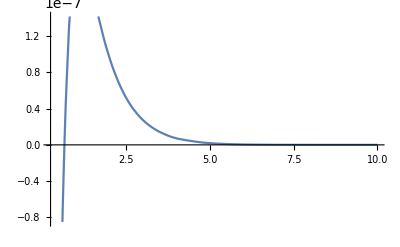

```mathematica
Plot[conversion*colliderrate[x],{x,0.25,10}]
```

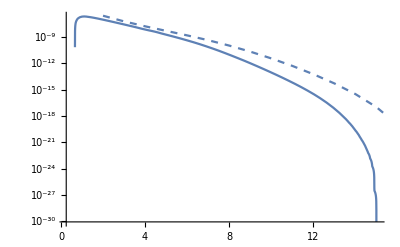

```mathematica
Show[Quiet[LogPlot[conversion*colliderrate[x],{x,0.25,Sqrt[comsquared]}]],ListLogPlot[{{#[[1]],#[[3]](246/1000000)^2}&/@xsinputs[[2]]},Joined->True,Frame->True,PlotStyle->{Dashed}]]
```

```mathematica
Show[Quiet[Plot[conversion*colliderrate[x],{x,0.25,Sqrt[comsquared]},PlotRange->{0,10^-7}]],ListPlot[{{#[[1]],#[[3]](246/1000000)^2}&/@xsinputs[[2]]},Joined->True,Frame->True,PlotStyle->{Dashed}]]
```

-Graphics-

```mathematica
inputs=Table[{x,colliderrate[x]},{x,0.8,5,0.1}]
```

{{0.8,3.29047×10^-16},{0.9,4.7136×10^-16},{1.,5.52551×10^-16},{1.1,5.77188×10^-16},{1.2,5.58862×10^-16},{1.3,5.1636×10^-16},{1.4,4.77767×10^-16},{1.5,4.34745×10^-16},{1.6,3.92248×10^-16},{1.7,3.51763×10^-16},{1.8,3.14044×10^-16},{1.9,2.79411×10^-16},{2.,2.48018×10^-16},{2.1,2.19663×10^-16},{2.2,1.94287×10^-16},{2.3,1.71665×10^-16},{2.4,1.51446×10^-16},{2.5,1.33632×10^-16},{2.6,1.17712×10^-16},{2.7,1.03617×10^-16},{2.8,9.12494×10^-17},{2.9,8.0257×10^-17},{3.,7.05153×10^-17},{3.1,6.19716×10^-17},{3.2,5.45139×10^-17},{3.3,4.78282×10^-17},{3.4,4.19522×10^-17},{3.5,3.68055×10^-17},{3.6,3.23121×10^-17},{3.7,2.8119×10^-17},{3.8,2.43466×10^-17},{3.9,2.11901×10^-17},{4.,1.85677×10^-17},{4.1,1.6407×10^-17},{4.2,1.46445×10^-17},{4.3,1.30713×10^-17},{4.4,1.1571×10^-17},{4.5,1.01463×10^-17},{4.6,8.80065×10^-18},{4.7,7.53819×10^-18},{4.8,6.42114×10^-18},{4.9,5.57753×10^-18},{5.,4.83977×10^-18}}

```mathematica
observableratenew[faPeV_,mass_,rate_,averageboostfactor_]:=kfactor*rate(1/faPeV)^2 *300*10^20/(80*10^9)*decayprobability[InverseEVtoMeter*faPeV^2/(Widthfunc[mass]*10^9)*averageboostfactor,579,2.5*2*2]
```

```mathematica
Plot[averageboostfactorfunc[x],{x,0.3,15},PlotRange->Full]
{#[[1]],Maximize[observableratenew[faPeV,#[[1]],conversion#[[2]],rapiditytogamma[averageboostfactorfunc[#[[1]]]]],faPeV]}&/@inputs[[1;;20]]
{#[[1]],#[[2,1]],#[[2,2,1]],InverseEVtoMeter*faPeV^2/(Widthfunc[#[[1]]]*10^9)*rapiditytogamma[averageboostfactorfunc[#[[1]]]]/.#[[2,2,1]]}&/@%
```

-Graphics-

{{0.8,{1.22459×10^6,{faPeV→0.0165515}}},{0.9,{56762.7,{faPeV→0.0920131}}},{1.,{14008.1,{faPeV→0.20054}}},{1.1,{8336.45,{faPeV→-0.265689}}},{1.2,{1565.77,{faPeV→0.603245}}},{1.3,{397.302,{faPeV→-1.15112}}},{1.4,{130.649,{faPeV→-1.9309}}},{1.5,{52.8904,{faPeV→-2.8949}}},{1.6,{26.1116,{faPeV→-3.91353}}},{1.7,{15.262,{faPeV→-4.84758}}},{1.8,{11.6825,{faPeV→5.2352}}},{1.9,{7.0675,{faPeV→-6.34883}}},{2.,{4.14284,{faPeV→-7.81262}}},{2.1,{2.53467,{faPeV→9.39989}}},{2.2,{1.61426,{faPeV→11.0775}}},{2.3,{1.06556,{faPeV→12.8161}}},{2.4,{0.724855,{faPeV→14.5952}}},{2.5,{0.507812,{faPeV→-16.3798}}},{2.6,{0.363637,{faPeV→-18.1669}}},{2.7,{0.265843,{faPeV→-19.9346}}}}

{{0.8,1.22459×10^6,faPeV→0.0165515,290.746},{0.9,56762.7,faPeV→0.0920131,290.746},{1.,14008.1,faPeV→0.20054,290.746},{1.1,8336.45,faPeV→-0.265689,290.746},{1.2,1565.77,faPeV→0.603245,290.746},{1.3,397.302,faPeV→-1.15112,290.746},{1.4,130.649,faPeV→-1.9309,290.746},{1.5,52.8904,faPeV→-2.8949,290.746},{1.6,26.1116,faPeV→-3.91353,290.746},{1.7,15.262,faPeV→-4.84758,290.746},{1.8,11.6825,faPeV→5.2352,290.746},{1.9,7.0675,faPeV→-6.34883,290.746},{2.,4.14284,faPeV→-7.81262,290.746},{2.1,2.53467,faPeV→9.39989,290.746},{2.2,1.61426,faPeV→11.0775,290.746},{2.3,1.06556,faPeV→12.8161,290.746},{2.4,0.724855,faPeV→14.5952,290.746},{2.5,0.507812,faPeV→-16.3798,290.746},{2.6,0.363637,faPeV→-18.1669,290.746},{2.7,0.265843,faPeV→-19.9346,290.746}}

```mathematica
limitsolutions={#[[1]],NSolve[observableratenew[faPeV,#[[1]],conversion#[[2]],rapiditytogamma[averageboostfactorfunc[#[[1]]]]]==3,faPeV,Reals]}&/@inputs[[1;;20]]
```

{{0.8,{{faPeV→-0.820111},{faPeV→-0.0052144},{faPeV→0.0052144},{faPeV→0.820111}}},{0.9,{{faPeV→-2.11387},{faPeV→-0.031824},{faPeV→0.031824},{faPeV→2.11387}}},{1.,{{faPeV→-3.24406},{faPeV→-0.0729211},{faPeV→0.0729211},{faPeV→3.24406}}},{1.1,{{faPeV→-3.77279},{faPeV→-0.0985761},{faPeV→0.0985761},{faPeV→3.77279}}},{1.2,{{faPeV→-5.62068},{faPeV→-0.240571},{faPeV→0.240571},{faPeV→5.62068}}},{1.3,{{faPeV→-7.56801},{faPeV→-0.4924},{faPeV→0.4924},{faPeV→7.56801}}},{1.4,{{faPeV→-9.52694},{faPeV→-0.883414},{faPeV→0.883414},{faPeV→9.52694}}},{1.5,{{faPeV→-11.2503},{faPeV→-1.41283},{faPeV→1.41283},{faPeV→11.2503}}},{1.6,{{faPeV→-12.5517},{faPeV→-2.02667},{faPeV→2.02667},{faPeV→12.5517}}},{1.7,{{faPeV→-13.3613},{faPeV→-2.64586},{faPeV→2.64586},{faPeV→13.3613}}},{1.8,{{faPeV→-13.3472},{faPeV→-2.94265},{faPeV→2.94265},{faPeV→13.3472}}},{1.9,{{faPeV→-13.8848},{faPeV→-3.80176},{faPeV→3.80176},{faPeV→13.8848}}},{2.,{{faPeV→-14.2914},{faPeV→-5.09194},{faPeV→5.09194},{faPeV→14.2914}}},{2.1,{{faPeV→-14.1637},{faPeV→-6.83429},{faPeV→6.83429},{faPeV→14.1637}}},{2.2,{{faPeV→-12.6801},{faPeV→-9.82444},{faPeV→9.82444},{faPeV→12.6801}}},{2.3,{}},{2.4,{}},{2.5,{}},{2.6,{}},{2.7,{}}}

```mathematica
limitsolutions1event={#[[1]],NSolve[observableratenew[faPeV,#[[1]],conversion#[[2]],rapiditytogamma[averageboostfactorfunc[#[[1]]]]]==1,faPeV,Reals]}&/@inputs[[1;;20]]
```

{{0.8,{{faPeV→-1.07942},{faPeV→-0.00506448},{faPeV→0.00506448},{faPeV→1.07942}}},{0.9,{{faPeV→-2.78313},{faPeV→-0.0307087},{faPeV→0.0307087},{faPeV→2.78313}}},{1.,{{faPeV→-4.27289},{faPeV→-0.0700767},{faPeV→0.0700767},{faPeV→4.27289}}},{1.1,{{faPeV→-4.97051},{faPeV→-0.0945611},{faPeV→0.0945611},{faPeV→4.97051}}},{1.2,{{faPeV→-7.41546},{faPeV→-0.229119},{faPeV→0.229119},{faPeV→7.41546}}},{1.3,{{faPeV→-10.0097},{faPeV→-0.465086},{faPeV→0.465086},{faPeV→10.0097}}},{1.4,{{faPeV→-12.6506},{faPeV→-0.826581},{faPeV→0.826581},{faPeV→12.6506}}},{1.5,{{faPeV→-15.0241},{faPeV→-1.30789},{faPeV→1.30789},{faPeV→15.0241}}},{1.6,{{faPeV→-16.8836},{faPeV→-1.85466},{faPeV→1.85466},{faPeV→16.8836}}},{1.7,{{faPeV→-18.123},{faPeV→-2.3929},{faPeV→2.3929},{faPeV→18.123}}},{1.8,{{faPeV→-18.2049},{faPeV→-2.64184},{faPeV→2.64184},{faPeV→18.2049}}},{1.9,{{faPeV→-19.2134},{faPeV→-3.35251},{faPeV→3.35251},{faPeV→19.2134}}},{2.,{{faPeV→-20.2852},{faPeV→-4.36063},{faPeV→4.36063},{faPeV→20.2852}}},{2.1,{{faPeV→-21.0361},{faPeV→-5.57274},{faPeV→5.57274},{faPeV→21.0361}}},{2.2,{{faPeV→-21.3994},{faPeV→-7.0254},{faPeV→7.0254},{faPeV→21.3994}}},{2.3,{{faPeV→-21.2787},{faPeV→-8.79938},{faPeV→8.79938},{faPeV→21.2787}}},{2.4,{{faPeV→-20.4405},{faPeV→-11.1236},{faPeV→11.1236},{faPeV→20.4405}}},{2.5,{{faPeV→-17.1239},{faPeV→-15.753},{faPeV→15.753},{faPeV→17.1239}}},{2.6,{}},{2.7,{}}}

```mathematica
Show[
ListPlot[Flatten[{List[{#[[1]],Abs[faPeV]/.#[[2,1]]}&/@limitsolutions1event[[1;;18]]][[1]],ReverseSortBy[List[{#[[1]],Abs[faPeV]/.#[[2,2]]}&/@limitsolutions1event[[1;;18]]][[1]],1]},1],Joined->True,Frame->True,PlotStyle->Dashed,FrameLabel->{"mA (GeV)","fa (PeV)"},BaseStyle->16,ImageSize->600,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.2,0.8}]]],ListPlot[Flatten[{List[{#[[1]],Abs[faPeV]/.#[[2,1]]}&/@limitsolutions[[1;;15]]][[1]],ReverseSortBy[List[{#[[1]],Abs[faPeV]/.#[[2,2]]}&/@limitsolutions[[1;;15]]][[1]],1]},1],Joined->True,Frame->True,FrameLabel->{"mA (GeV)","fa (PeV)"},BaseStyle->16,ImageSize->600,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.2,0.8}]]]]
```

-Graphics-

What’s the effective decay volume for such energetic particles?

r=2.5, d=5m+5m

## More detailed calculation (slower) with simulations and particle momentum spread (checks)

```mathematica
protonmass=0.938;
teamenergy=120;
comsquared=(teamenergy+protonmass)^2-(teamenergy^2-protonmass^2);
Sqrt[%]
conversion=0.3894*10^9;(*from GeV^-2 to pb*)
decaygluon[x_]:=alphas[x^2,0,0][[1,1]]^2/(32Pi^3) x^3/(1000000)^2
partonrate[x_]:=1/(1/(2x)1/(16Pi)*8)*1/(2x^2)/(8*8*2*2)*(8)*2Pi/x^2decaygluon[x]
labframerap=1/2Log[(teamenergy+protonmass+Sqrt[teamenergy^2-protonmass^2])/(teamenergy+protonmass-Sqrt[teamenergy^2-protonmass^2])]
```

15.0625

2.77231

```mathematica
Log[(teamenergy+protonmass+Sqrt[teamenergy^2-protonmass^2])/(teamenergy+protonmass-Sqrt[teamenergy^2-protonmass^2])]
```

5.54463

```mathematica
E^5.5//N
```

244.692

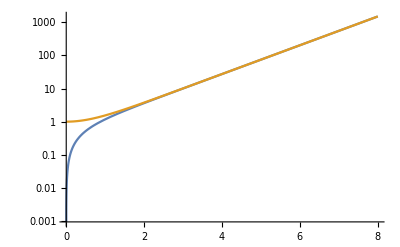

```mathematica
LogPlot[{rapiditytogammabeta[y],rapiditytogamma[y]},{y,0,8}]
```

```mathematica
grandfunctionpermasspoint[mass_,detectorlength_,statistics_,faPeV_]:=
Module[{xx,eventrapidity,eventrapidityabs,pdfweight,eventweight,components},
components=
Table[Total[Table[xx=RandomReal[{mass^2/comsquared,1}];
pdfweight=xPDFcv[xx,mass^2,0]xPDFcv[mass^2/comsquared/xx,mass^2,0]/xx;
eventrapidity=1/2Log[xx^2/(mass^2/comsquared)];
eventrapidityabs=1/2Abs[Log[xx^2/(mass^2/comsquared)]];
{eventweight=pdfweight*partonrate[mass]*conversion*kfactor*(1/faPeV)^2 *300*10^20/(80*10^9)*decayprobability[InverseEVtoMeter*faPeV^2/(WidthFunc[mass]*10^9)*rapiditytogammabeta[eventrapidity+labframerap],579,detectorlength],eventrapidity,pdfweight,eventrapidityabs},{i,1,statistics/10}]]*(1-mass^2/comsquared)/(statistics/10),{j,1,10}];
{mass,faPeV,Mean[#[[1]]&/@components],StandardDeviation[#[[1]]&/@components],detectorlength,Mean[#[[3]]&/@components],StandardDeviation[#[[3]]&/@components],Mean[#[[2]]*#[[3]]&/@components]/Mean[#[[3]]&/@components],StandardDeviation[#[[2]]*#[[3]]&/@components]/Mean[#[[3]]&/@components],Mean[#[[4]]*#[[3]]&/@components]/Mean[#[[3]]&/@components],StandardDeviation[#[[4]]*#[[3]]&/@components]/Mean[#[[3]]&/@components]}
];
```

```mathematica
simulationresults=Table[Table[Quiet[grandfunctionpermasspoint[masslist,10,10^4,faPeV]],{faPeV,{0.0001,0.0002,0.0005,0.001,0.002,0.005,0.008,0.01,0.02,0.05,0.08,0.1,0.2,0.5,0.8,1,1.5,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50}}],{masslist,{0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,mEtap,0.96,0.98,1.0,1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5,1.6,1.7,1.8,2.0,2.2,2.4,2.6,2.8,3.0}}];
```

```mathematica
Export[NotebookDirectory[]<>"simulationresult.m",simulationresults]
```

C:\Users\novar\Dropbox\Axion@DUNEND\research\simulationresult.m

```mathematica
simulationresults=Import[NotebookDirectory[]<>"simulationresult.m"];
```

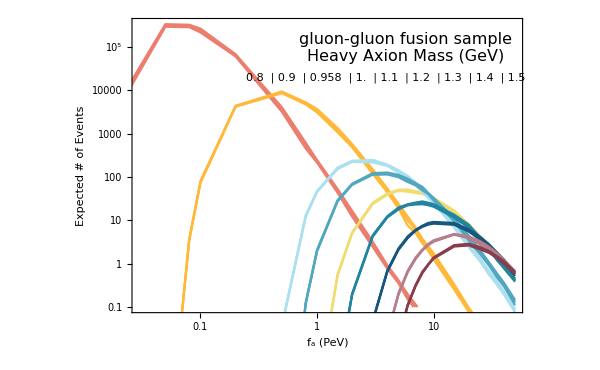

```mathematica
colorselecitonumber=24;
rescalefactoroflumi=147/300;
Show[
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[1]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[1]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[1]]},Joined->True,PlotRange->{{3*10^-2,50},{10^-1,Full}},PlotStyle->ColorData[colorselecitonumber,1],ImageSize->600,Frame->True,BaseStyle->20,FrameLabel->{{"Expected # of Events",""},{"f_a (PeV)","DUNE Near Detector 1.47×10^22 POT"}},FrameTicks->{{LogTicks[10,10^-8,10^6,TickLabelStep->2,ShowMinorTicks-> False],StripTickLabels[LogTicks[10,10^-8,10^6,TickLabelStep->2,ShowMinorTicks-> False]]},{Automatic,Automatic}}],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[6]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[6]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[6]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,2]],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[9]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[9]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[9]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,3]],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[12]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[12]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[12]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,4]],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[17]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[17]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[17]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,5]],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[22]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[22]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[22]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,6]],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[27]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[27]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[27]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,7]],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[32]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[32]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[32]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,8]],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[37]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[37]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[37]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,9]](*,
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[10]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[10]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[10]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,10]],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[11]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[11]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[11]]},Joined->True,PlotRange->Full,PlotStyle->ColorData[colorselecitonumber,11]]*),
Epilog->{Inset[Grid[Table[Style[If[j==0,{0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,mEtap,0.96,0.98,1.0,1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5,1.6,1.7,1.8,2.0,2.2,2.4,2.6,2.8,3.0}[[{1,6,9,12,17,22,27,32,37}[[i]]]]If[i≠9,"",""],"GeV"],ColorData[colorselecitonumber][i],FontSize->16,Bold],{j,0,0,1},{i,1,9,1}]],Scaled[{0.65,0.8}]],Inset[Style["gluon-gluon fusion sample\nHeavy Axion Mass (GeV)",16],Scaled[{0.7,0.9}]]}
]
```

```mathematica
Table[Style[If[j==0,{0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,mEtap,0.96,0.98,1.0,1.02,1.04,1.06,1.08,1.1,1.12,1.14,1.16,1.18,1.2,1.22,1.24,1.26,1.28,1.3,1.32,1.34,1.36,1.38,1.4,1.42,1.44,1.46,1.48,1.5,1.6,1.7,1.8,2.0,2.2,2.4,2.6,2.8,3.0}[[{1,6,9,12,17,22,27,32,37}[[i]]]]<>If[i≠9,",",""],"GeV"],ColorData[colorselecitonumber][i],FontSize->16,Bold],{j,0,0,1},{i,1,9,1}]
```

StringJoin::string: String expected at position 1 in 0.8<>,.

StringJoin::string: String expected at position 1 in 0.9<>,.

StringJoin::string: String expected at position 1 in 0.958<>,.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

{{0.8<>,,0.9<>,,0.958<>,,1.<>,,1.1<>,,1.2<>,,1.3<>,,1.4<>,,StringJoin[1.5]}}

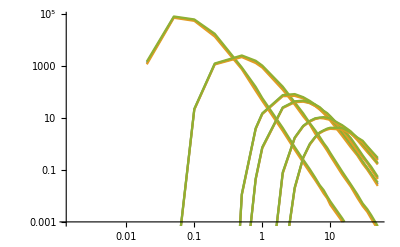

```mathematica
(*A seperate run's result*)
Show[
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[1]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[1]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[1]]},Joined->True,PlotRange->{10^-3,Full}],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[2]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[2]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[2]]},Joined->True,PlotRange->Full],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[3]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[3]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[3]]},Joined->True,PlotRange->Full],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[4]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[4]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[4]]},Joined->True,PlotRange->Full],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[5]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[5]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[5]]},Joined->True,PlotRange->Full],
ListLogLogPlot[{{#[[2]],#[[3]]}&/@simulationresults[[6]],{#[[2]],#[[3]]-#[[4]]}&/@simulationresults[[6]],{#[[2]],#[[3]]+#[[4]]}&/@simulationresults[[6]]},Joined->True,PlotRange->Full]
]
```

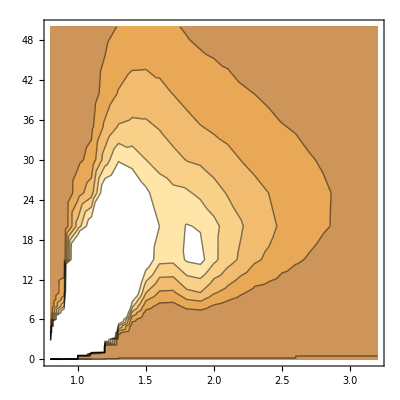

```mathematica
ListContourPlot[Flatten[Table[{#[[1]],#[[2]],#[[3]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1],InterpolationOrder->1]
```

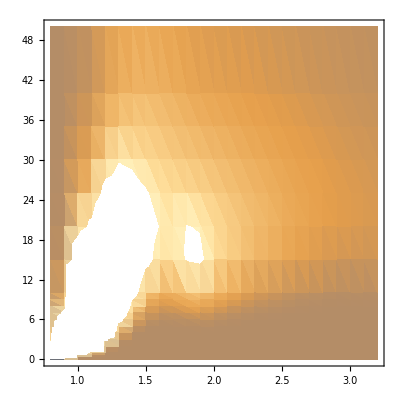

```mathematica
ListDensityPlot[Flatten[Table[{#[[1]],#[[2]],#[[3]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1]]
```

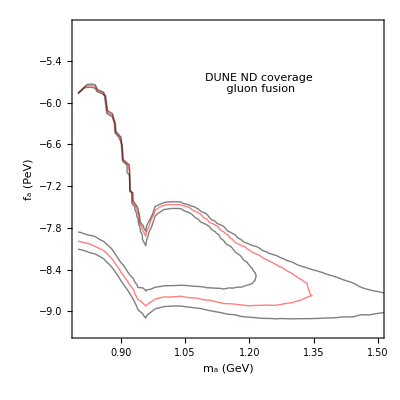

```mathematica
ListContourPlot[Flatten[Table[{#[[1]],Log[10,1/(4Pi^2#[[2]]*10^6)],Log[144/300#[[3]]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1],Contours->{0,Log[3],Log[10]},PlotRange->{{0.8,1.5},Automatic},ContourStyle->{Thick,Red},ContourShading->{None},InterpolationOrder->All,FrameLabel->{"m_a (GeV)","f_a (PeV)"},BaseStyle->16,ImageSize->400,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.6,0.8}]]]
```

Do we have room for a separate detector near the decay pipe?

### Numerical integral checks

```mathematica
Quiet[Table[{rs,NIntegrate[xPDFcv[xx,rs^2,0]xPDFcv[rs^2/comsquared/xx,rs^2,0]/xx,{xx,rs^2/comsquared,1}],NIntegrate[1/2Log[xx^2/(rs^2/comsquared)]xPDFcv[xx,rs^2,0]xPDFcv[rs^2/comsquared/xx,rs^2,0]/xx,{xx,rs^2/comsquared,1}],NIntegrate[1/2Abs[Log[xx^2/(rs^2/comsquared)]]xPDFcv[xx,rs^2,0]xPDFcv[rs^2/comsquared/xx,rs^2,0]/xx,{xx,rs^2/comsquared,1}]},{rs,{0.8,0.9,5}}]]
```

{{0.8,3.12598,6.61363×10^-17,2.29916},{0.9,4.70834,-1.43115×10^-17,3.68967},{5,0.0174717,-5.59042×10^-20,0.0041739}}

```mathematica
grandfunctionpermasspoint[mass_,detectorlength_,statistics_,faPeV_]:=
Module[{xx,eventrapidity,eventrapidityabs,pdfweight,eventweight,components},
components=
Table[Total[Table[xx=RandomReal[{mass^2/comsquared,1}];
pdfweight=xPDFcv[xx,mass^2,0]xPDFcv[mass^2/comsquared/xx,mass^2,0]/xx;
eventrapidity=1/2Log[xx^2/(mass^2/comsquared)];
eventrapidityabs=1/2Abs[Log[xx^2/(mass^2/comsquared)]];
{eventweight=pdfweight*partonrate[mass]*conversion*kfactor*(1/faPeV)^2 *300*10^20/(80*10^9)*decayprobability[InverseEVtoMeter*faPeV^2/(WidthFunc[mass]*10^9)*rapiditytogammabeta[eventrapidity+labframerap],579,detectorlength],eventrapidity*pdfweight,pdfweight,eventrapidityabs*pdfweight},{i,1,statistics/10}]]*(1-mass^2/comsquared)/(statistics/10),{j,1,10}];
{mass,faPeV,Mean[#[[1]]&/@components],StandardDeviation[#[[1]]&/@components],detectorlength,Mean[#[[3]]&/@components],StandardDeviation[#[[3]]&/@components],Mean[#[[2]]&/@components],StandardDeviation[#[[2]]&/@components],Mean[#[[4]]&/@components],StandardDeviation[#[[4]]&/@components]}
];
Quiet[grandfunctionpermasspoint[0.8,10,10^5,1]]
Quiet[grandfunctionpermasspoint[0.9,10,10^5,1]]
Quiet[grandfunctionpermasspoint[5,10,10^5,1]]
```

{0.8,1,268.121,5.04611,10,3.11051,0.0591892,0.032891,0.0562506,2.27748,0.0643952}

{0.9,1,96.7909,3.00638,10,4.75834,0.124859,-0.0439529,0.13606,3.74888,0.104117}

{5,1,0.,0.,10,0.0175964,0.000311702,-0.0000317336,0.0000867184,0.00419209,0.0000673298}

```mathematica
pseudodatagenerator[mass_,detectorlength_,statistics_,faPeV_]:=
Module[{xx,eventrapidity,eventrapidityabs,pdfweight,eventweight,components},
components=
Table[xx=RandomReal[{mass^2/comsquared,1}];
pdfweight=xPDFcv[xx,mass^2,0]xPDFcv[mass^2/comsquared/xx,mass^2,0]/xx;
eventrapidity=1/2Log[xx^2/(mass^2/comsquared)];
eventrapidityabs=1/2Abs[Log[xx^2/(mass^2/comsquared)]];
{eventweight=pdfweight*partonrate[mass]*conversion*kfactor*(1/faPeV)^2 *300*10^20/(80*10^9)*decayprobability[InverseEVtoMeter*faPeV^2/(WidthFunc[mass]*10^9)*rapiditytogammabeta[eventrapidity+labframerap],579,detectorlength],eventrapidity,pdfweight},{i,1,statistics}]
];
```

General::munfl: 4.41162×10^-8 5.61997×10^-304 is too small to represent as a normalized machine number; precision may be lost.

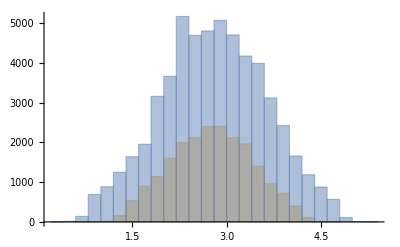

```mathematica
tempdata=pseudodatagenerator[1.2,10,10000,1];
WeightedData[#[[2]]+labframerap&/@tempdata,#[[3]]&/@tempdata];
tempdata=pseudodatagenerator[2,10,10000,1];
WeightedData[#[[2]]+labframerap&/@tempdata,#[[3]]&/@tempdata];
Histogram[{%,%%%}]
```

### Making plot

```mathematica
Show[
ListPlot[Flatten[{List[{#[[1]],Abs[faPeV]/.#[[2,1]]}&/@limitsolutions1event[[1;;18]]][[1]],ReverseSortBy[List[{#[[1]],Abs[faPeV]/.#[[2,2]]}&/@limitsolutions1event[[1;;18]]][[1]],1]},1],Joined->True,Frame->True,PlotStyle->Dashed,FrameLabel->{"mA (GeV)","fa (PeV)"},BaseStyle->16,ImageSize->600,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.2,0.8}]]],ListPlot[Flatten[{List[{#[[1]],Abs[faPeV]/.#[[2,1]]}&/@limitsolutions[[1;;15]]][[1]],ReverseSortBy[List[{#[[1]],Abs[faPeV]/.#[[2,2]]}&/@limitsolutions[[1;;15]]][[1]],1]},1],Joined->True,Frame->True,FrameLabel->{"mA (GeV)","fa (PeV)"},BaseStyle->16,ImageSize->600,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.2,0.8}]]]]
```

-Graphics-

## More detailed calculation (slower) with simulations and particle momentum spread (checks) for differential distributions

```mathematica
protonmass=0.938;
teamenergy=120;
comsquared=(teamenergy+protonmass)^2-(teamenergy^2-protonmass^2);
Sqrt[%]
conversion=0.3894*10^9;(*from GeV^-2 to pb*)
decaygluon[x_]:=alphas[x^2,0,0][[1,1]]^2/(32Pi^3) x^3/(1000000)^2
partonrate[x_]:=1/(1/(2x)1/(16Pi)*8)*1/(2x^2)/(8*8*2*2)*(8)*2Pi/x^2decaygluon[x]
labframerap=1/2Log[(teamenergy+protonmass+Sqrt[teamenergy^2-protonmass^2])/(teamenergy+protonmass-Sqrt[teamenergy^2-protonmass^2])]
```

15.0625

2.77231

```mathematica
Log[(teamenergy+protonmass+Sqrt[teamenergy^2-protonmass^2])/(teamenergy+protonmass-Sqrt[teamenergy^2-protonmass^2])]
```

5.54463

```mathematica
E^5.5//N
```

244.692

```mathematica
LogPlot[{rapiditytogammabeta[y],rapiditytogamma[y]},{y,0,8}]
```

-Graphics-

```mathematica
simulationbeforecut[mass_,detectorlength_,statistics_,faPeV_]:=
Module[{xx,eventrapidity,eventrapidityabs,pdfweight,eventweight,components},
components=
Table[xx=RandomReal[{mass^2/comsquared,1}];
pdfweight=xPDFcv[xx,mass^2,0]xPDFcv[mass^2/comsquared/xx,mass^2,0]/xx;
eventrapidity=1/2Log[xx^2/(mass^2/comsquared)];
eventrapidityabs=1/2Abs[Log[xx^2/(mass^2/comsquared)]];
{rapiditytogamma[eventrapidity+labframerap]mass,pdfweight*(1-mass^2/comsquared)*partonrate[mass]*conversion*kfactor*(1/faPeV)^2 *300*10^20/(80*10^9)},{i,1,statistics}]
];
simulationaftercut[mass_,detectorlength_,statistics_,faPeV_]:=
Module[{xx,eventrapidity,eventrapidityabs,pdfweight,eventweight,components},
components=
Table[xx=RandomReal[{mass^2/comsquared,1}];
pdfweight=xPDFcv[xx,mass^2,0]xPDFcv[mass^2/comsquared/xx,mass^2,0]/xx;
eventrapidity=1/2Log[xx^2/(mass^2/comsquared)];
eventrapidityabs=1/2Abs[Log[xx^2/(mass^2/comsquared)]];
{rapiditytogamma[eventrapidity+labframerap]mass,pdfweight*(1-mass^2/comsquared)*partonrate[mass]*conversion*kfactor*(1/faPeV)^2 *300*10^20/(80*10^9)decayprobability[InverseEVtoMeter*faPeV^2/(WidthFunc[mass]*10^9)*rapiditytogammabeta[eventrapidity+labframerap],579,detectorlength]},{i,1,statistics}]
];
```

```mathematica
beforecutdata[mass_,detectorlength_,statistics_,faPeV_]:=(tempdata=simulationbeforecut[mass,detectorlength,statistics,faPeV];totalweight=Total[Chop[If[#[[2]]>0,#[[2]],0]]&/@tempdata];WeightedData[#[[1]]&/@tempdata,Chop[If[#[[2]]>0,#[[2]],0]/totalweight]&/@tempdata])
aftercutdata[mass_,detectorlength_,statistics_,faPeV_]:=(tempdata=simulationaftercut[mass,detectorlength,statistics,faPeV];totalweight=Total[Chop[If[#[[2]]>0,#[[2]],0]]&/@tempdata];WeightedData[#[[1]]&/@tempdata,Chop[If[#[[2]]>0,#[[2]],0]/totalweight]&/@tempdata])
```

General::munfl: 4.82749×10^-6 4.86116×10^-304 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.79951×10^-6 1.12725×10^-306 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.80417×10^-6 3.32383×10^-306 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

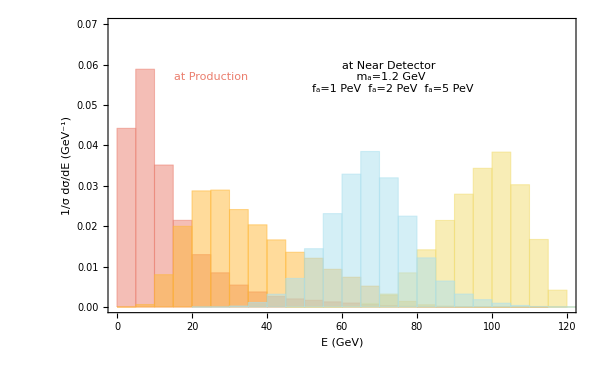

```mathematica
Histogram[{beforecutdata[1.2,10,10^5,500/(4Pi^2)],aftercutdata[1.2,10,10^5,200/(4Pi^2)],aftercutdata[1.2,10,10^5,50/(4Pi^2)],aftercutdata[1.2,10,10^5,2]},20,"PDF",PlotRange->{{0,120},{0,0.07}},Frame->True,PlotRangePadding->0,PerformanceGoal->"Quality",BarOrigin->Bottom,ChartStyle->colorselecitonumber,ImageSize->600,Frame->True,BaseStyle->20,FrameLabel->{{"1/σ dσ/dE (GeV^-1)",""},{"E (GeV)",""}},Epilog->{Inset["at Near Detector\n m_a=1.2 GeV\n"Style[" f_a=5 PeV", ColorData[colorselecitonumber][2]]Style[" f_a=2 PeV", ColorData[colorselecitonumber][4]]Style[" f_a=1 PeV", ColorData[colorselecitonumber][3]],Scaled[{0.6,0.8}]],Inset[Style["at Production", ColorData[colorselecitonumber][1]],Scaled[{0.22,0.8}]]}]
```

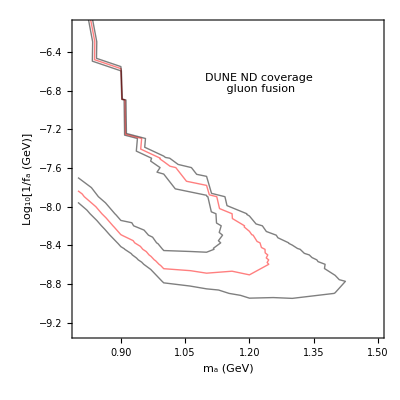

```mathematica
ListContourPlot[Flatten[Table[{#[[1]],Log[10,1/(4Pi^2#[[2]]*10^6)],Log[144/300#[[3]]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1],Contours->{0,Log[3],Log[10]},PlotRange->{{0.8,1.5},Automatic},ContourStyle->{Thick,Red},ContourShading->{None},InterpolationOrder->All,FrameLabel->{"m_a (GeV)","Log_10[1/f_a (GeV)]"},BaseStyle->16,ImageSize->400,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.6,0.8}]]]
```

```mathematica
Contours
```

Do we have room for a separate detector near the decay pipe?

## Code/Data for final reach plot

```mathematica
simulationresults=Import[NotebookDirectory[]<>"simulationresult.m"];
```

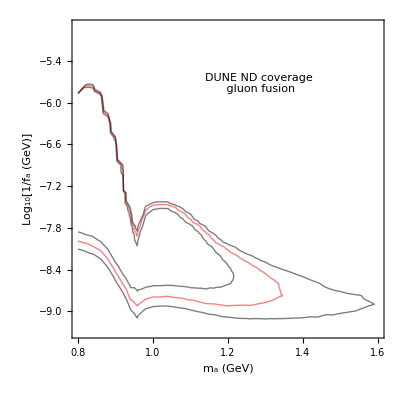

```mathematica
ListContourPlot[Flatten[Table[{#[[1]],Log[10,1/(4Pi^2#[[2]]*10^6)],Log[144/300#[[3]]]}&/@simulationresults[[i]],{i,1,Length[simulationresults]}],1],Contours->{0,Log[3],Log[10]},PlotRange->{{0.8,1.6},Automatic},ContourStyle->{Thick,Red},ContourShading->{None},InterpolationOrder->1,FrameLabel->{"m_a (GeV)","Log_10[1/f_a (GeV)]"},BaseStyle->16,ImageSize->400,Epilog->Inset["DUNE ND coverage\n gluon fusion",Scaled[{0.6,0.8}]]]
```

## Data for distribution plot

```mathematica
datagenbeforecutdata[mass_,detectorlength_,statistics_,faPeV_]:=(tempdata=simulationbeforecut[mass,detectorlength,statistics,faPeV];totalweight=Total[Chop[If[#[[2]]>0,#[[2]],0]]&/@tempdata];{#[[1]],tempcosstar=RandomReal[{-1,1}];angl1=2ArcTan[1/Exp[1/2Log[(1+tempcosstar)/(1-tempcosstar)]+gammatorapidityPzonly[#[[1]]/mass]]];angl2=2ArcTan[1/Exp[1/2Log[(1-tempcosstar)/(1+tempcosstar)]+gammatorapidityPzonly[#[[1]]/mass]]];(angl1+angl2)*180/Pi,Chop[If[#[[2]]>0,#[[2]],0]/totalweight]}&/@tempdata)
datagenaftercutdata[mass_,detectorlength_,statistics_,faPeV_]:=(tempdata=simulationaftercut[mass,detectorlength,statistics,faPeV];totalweight=Total[Chop[If[#[[2]]>0,#[[2]],0]]&/@tempdata];{#[[1]],tempcosstar=RandomReal[{-1,1}];angl1=2ArcTan[1/Exp[1/2Log[(1+tempcosstar)/(1-tempcosstar)]+gammatorapidityPzonly[#[[1]]/mass]]];angl2=2ArcTan[1/Exp[1/2Log[(1-tempcosstar)/(1+tempcosstar)]+gammatorapidityPzonly[#[[1]]/mass]]];(angl1+angl2)*180/Pi,Chop[If[#[[2]]>0,#[[2]],0]/totalweight]}&/@tempdata)
```

```mathematica
tempdata1=datagenbeforecutdata[1.2,10,10^6,50/(4Pi^2)];
tempdata2=datagenaftercutdata[1.2,10,10^6,50/(4Pi^2)];
tempdata3=datagenaftercutdata[1.2,10,10^6,100/(4Pi^2)];
tempdata4=datagenaftercutdata[1.2,10,10^6,200/(4Pi^2)];
```

General::munfl: 3.07619×10^-6 5.80484×10^-305 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.07671×10^-6 2.13399×10^-305 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.07405×10^-6 5.06873×10^-303 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: (1.57895×10^-307)/625 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.60559×10^-9 1.68582×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.82802×10^-307)/625 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"ggFdata_Production_1.2GeV.csv",tempdata1,"CSV"]
Export[NotebookDirectory[]<>"ggFdata_Detection_1.2GeV_1PeV.csv",tempdata2,"CSV"]
Export[NotebookDirectory[]<>"ggFdata_Detection_1.2GeV_2PeV.csv",tempdata3,"CSV"]
Export[NotebookDirectory[]<>"ggFdata_Detection_1.2GeV_5PeV.csv",tempdata4,"CSV"]
```

C:\Users\novar\Dropbox\Axion@DUNEND\research\ggFdata_Production_1.2GeV.csv

C:\Users\novar\Dropbox\Axion@DUNEND\research\ggFdata_Detection_1.2GeV_1PeV.csv

C:\Users\novar\Dropbox\Axion@DUNEND\research\ggFdata_Detection_1.2GeV_2PeV.csv

C:\Users\novar\Dropbox\Axion@DUNEND\research\ggFdata_Detection_1.2GeV_5PeV.csv

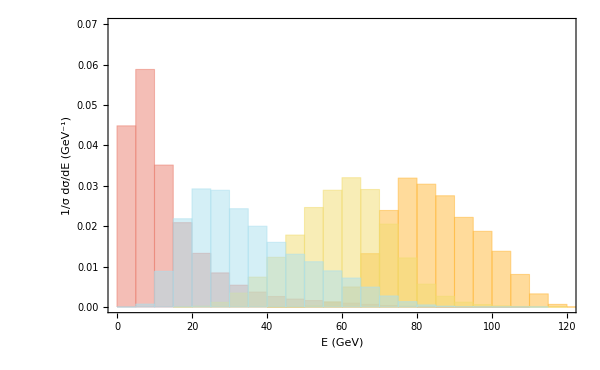

```mathematica
Histogram[{WeightedData[#[[1]]&/@tempdata1,#[[3]]&/@tempdata1],WeightedData[#[[1]]&/@tempdata2,#[[3]]&/@tempdata2],WeightedData[#[[1]]&/@tempdata3,#[[3]]&/@tempdata3],WeightedData[#[[1]]&/@tempdata4,#[[3]]&/@tempdata4]},20,"PDF",PlotRange->{{0,120},{0,0.07}},Frame->True,PlotRangePadding->0,PerformanceGoal->"Quality",BarOrigin->Bottom,ChartStyle->colorselecitonumber,ImageSize->600,Frame->True,BaseStyle->20,FrameLabel->{{"1/σ dσ/dE (GeV^-1)",""},{"E (GeV)","DUNE Near Detector 1.47×10^22 POT"}}]
```

```mathematica
Show[%153,Epilog->{Inset[Style["at Production", ColorData[colorselecitonumber][1]],Scaled[{0.2,0.8}]],Inset["Accepted by Near Detector\n m_a=1.2 GeV\n"Grid[{{Style[" f_G=200 PeV", ColorData[colorselecitonumber][4]],Style[" f_G=100 PeV", ColorData[colorselecitonumber][3]],Style[" f_G=50 PeV", ColorData[colorselecitonumber][2]]}}],Scaled[{0.6,0.8}]],Inset[Style["at Production", ColorData[colorselecitonumber][1]],Scaled[{0.2,0.8}]],Inset[Style["at Production", ColorData[colorselecitonumber][1]],Scaled[{0.2,0.8}]]}]
```